```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-12-20"}];
dropBoxfolder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox"}];
dropBoxfolderLaptop=FileNameJoin[{"/","home","karl","Dropbox"}];
dataFolder=FileNameJoin[{"00School","research","DataRuns"}];
folder=FileNameJoin[{dropBoxfolder,dataFolder}];
SetDirectory[folder];
FileNames[]
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,17-11-18_SystemDiagnosis,17-12-18_SystemDiagnosis,17-12-20_PolarizingElectrons,18-01-03_PolarizingElectrons,18-01-04_PolarizingElectrons,18-01-10_ChamberWarming,18-01-11_SystemDiagnostics,18-01-12_recreatingPolFigure,18-01-13_recreatingPolFigureIncreasedT,18-01-16_morePolarization,18-01-20_electronPolarization,18-01-25_excitationFunctions,18-01-28_bufferGasPressureVsCounts,18-01-28_exFnCurrentNormalized.png,18-01-28_exFnMolyCounts.png,18-01-28_exFnRawCounts.png,18-01-28_exFnSignalCounts.png,18-01-28_hayesReproduction,18-02-12_polarizedElectrons,18-02-13,18-02-14_scratchWork,18-02-15_addtlBGP,dataDump,test.png,wavemeterOffsets}

```mathematica
SetDirectory[FileNameJoin[{folder,"18-01-28_hayesReproduction","data"}]];
polFileNames=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]]
excitationFileNames=FileNames[StringExpression["EX",__,"_",__,DigitCharacter,".dat"]]
```

{POL2018-01-28_190002.dat,POL2018-01-28_190526.dat,POL2018-01-28_191053.dat,POL2018-01-28_191620.dat,POL2018-01-28_192146.dat,POL2018-01-28_192713.dat,POL2018-01-28_193240.dat,POL2018-01-28_193806.dat,POL2018-01-28_194333.dat,POL2018-01-28_194900.dat,POL2018-01-28_195428.dat,POL2018-01-28_195955.dat,POL2018-01-28_200522.dat,POL2018-01-28_201048.dat,POL2018-01-28_201615.dat,POL2018-01-28_202142.dat,POL2018-01-28_202708.dat,POL2018-01-28_203235.dat,POL2018-01-28_203802.dat,POL2018-01-28_204328.dat,POL2018-01-28_204855.dat,POL2018-01-28_205421.dat,POL2018-01-28_210222.dat,POL2018-01-28_210748.dat,POL2018-01-28_211315.dat,POL2018-01-28_211842.dat,POL2018-01-28_212408.dat,POL2018-01-28_212935.dat,POL2018-01-28_213502.dat,POL2018-01-28_214028.dat,POL2018-01-28_214555.dat,POL2018-01-28_215121.dat,POL2018-01-28_215648.dat,POL2018-01-28_220215.dat,POL2018-01-28_220741.dat,POL2018-01-28_221308.dat,POL2018-01-28_221834.dat,POL2018-01-28_222401.dat,POL2018-01-28_222928.dat,POL2018-01-28_223454.dat,POL2018-01-28_224021.dat,POL2018-01-28_224548.dat,POL2018-01-28_225114.dat,POL2018-01-28_225641.dat,POL2018-01-28_230442.dat,POL2018-01-28_231008.dat,POL2018-01-28_231535.dat,POL2018-01-28_232101.dat,POL2018-01-28_232628.dat,POL2018-01-28_233154.dat,POL2018-01-28_233721.dat,POL2018-01-28_234248.dat,POL2018-01-28_234814.dat,POL2018-01-28_235345.dat,POL2018-01-28_235912.dat,POL2018-01-29_000438.dat,POL2018-01-29_001005.dat,POL2018-01-29_001532.dat,POL2018-01-29_002058.dat,POL2018-01-29_002625.dat,POL2018-01-29_003151.dat,POL2018-01-29_003718.dat,POL2018-01-29_004245.dat,POL2018-01-29_004811.dat,POL2018-01-29_005338.dat,POL2018-01-29_005907.dat,POL2018-01-29_010433.dat,POL2018-01-29_011000.dat,POL2018-01-29_011527.dat,POL2018-01-29_012053.dat,POL2018-01-29_012620.dat,POL2018-01-29_013147.dat,POL2018-01-29_013713.dat,POL2018-01-29_014240.dat,POL2018-01-29_014806.dat,POL2018-01-29_015333.dat,POL2018-01-29_015900.dat,POL2018-01-29_020426.dat,POL2018-01-29_020953.dat,POL2018-01-29_021519.dat,POL2018-01-29_022046.dat,POL2018-01-29_022613.dat,POL2018-01-29_023139.dat,POL2018-01-29_023706.dat,POL2018-01-29_024233.dat,POL2018-01-29_024759.dat,POL2018-01-29_025326.dat,POL2018-01-29_025852.dat,POL2018-01-29_030419.dat,POL2018-01-29_030946.dat,POL2018-01-29_031512.dat,POL2018-01-29_032039.dat,POL2018-01-29_032606.dat,POL2018-01-29_033132.dat,POL2018-01-29_033659.dat,POL2018-01-29_034226.dat,POL2018-01-29_034752.dat,POL2018-01-29_035319.dat,POL2018-01-29_035845.dat,POL2018-01-29_040412.dat,POL2018-01-29_040939.dat,POL2018-01-29_041505.dat,POL2018-01-29_042032.dat,POL2018-01-29_042558.dat,POL2018-01-29_043125.dat,POL2018-01-29_043652.dat,POL2018-01-29_044218.dat,POL2018-01-29_044745.dat,POL2018-01-29_045312.dat,POL2018-01-29_045838.dat,POL2018-01-29_050405.dat,POL2018-01-29_050931.dat,POL2018-01-29_051458.dat,POL2018-01-29_052025.dat,POL2018-01-29_052551.dat,POL2018-01-29_053118.dat,POL2018-01-29_053645.dat,POL2018-01-29_054211.dat,POL2018-01-29_054738.dat,POL2018-01-29_055305.dat,POL2018-01-29_055831.dat,POL2018-01-29_060358.dat,POL2018-01-29_060925.dat,POL2018-01-29_061451.dat,POL2018-01-29_062018.dat,POL2018-01-29_062545.dat,POL2018-01-29_063111.dat,POL2018-01-29_063638.dat,POL2018-01-29_064204.dat,POL2018-01-29_064731.dat,POL2018-01-29_065258.dat,POL2018-01-29_065824.dat,POL2018-01-29_070351.dat,POL2018-01-29_070918.dat,POL2018-01-29_071444.dat,POL2018-01-29_072011.dat,POL2018-01-29_072537.dat,POL2018-01-29_073104.dat,POL2018-01-29_073631.dat,POL2018-01-29_074157.dat,POL2018-01-29_074724.dat,POL2018-01-29_075250.dat,POL2018-01-29_075817.dat,POL2018-01-29_080344.dat,POL2018-01-29_080910.dat,POL2018-01-29_081437.dat,POL2018-01-29_082004.dat,POL2018-01-29_082530.dat,POL2018-01-29_083057.dat,POL2018-01-29_083623.dat,POL2018-01-29_084150.dat,POL2018-01-29_084717.dat,POL2018-01-29_085243.dat,POL2018-01-29_085810.dat,POL2018-01-29_090337.dat,POL2018-01-29_090903.dat,POL2018-01-29_091430.dat,POL2018-01-29_091956.dat,POL2018-01-29_092523.dat,POL2018-01-29_093050.dat,POL2018-01-29_093616.dat,POL2018-01-29_094143.dat,POL2018-01-29_094710.dat,POL2018-01-29_095236.dat,POL2018-01-29_095803.dat,POL2018-01-29_100329.dat,POL2018-01-29_100856.dat,POL2018-01-29_101423.dat,POL2018-01-29_101949.dat,POL2018-01-29_102516.dat,POL2018-01-29_103043.dat,POL2018-01-29_103609.dat,POL2018-01-29_104136.dat,POL2018-01-29_104703.dat,POL2018-01-29_105229.dat,POL2018-01-29_105756.dat,POL2018-01-29_110322.dat,POL2018-01-29_110849.dat,POL2018-01-29_111416.dat,POL2018-01-29_111942.dat,POL2018-01-29_112509.dat,POL2018-01-29_113038.dat,POL2018-01-29_113605.dat,POL2018-01-29_114131.dat,POL2018-01-29_114658.dat,POL2018-01-29_115224.dat,POL2018-01-29_115751.dat,POL2018-01-29_120318.dat,POL2018-01-29_120844.dat,POL2018-01-29_121411.dat,POL2018-01-29_121938.dat,POL2018-01-29_122505.dat,POL2018-01-29_123031.dat,POL2018-01-29_123558.dat,POL2018-01-29_124125.dat,POL2018-01-29_124651.dat,POL2018-01-29_125218.dat,POL2018-01-29_125745.dat,POL2018-01-29_130311.dat,POL2018-01-29_130838.dat,POL2018-01-29_131404.dat,POL2018-01-29_131931.dat,POL2018-01-29_132458.dat,POL2018-01-29_133024.dat,POL2018-01-29_133551.dat,POL2018-01-29_134118.dat,POL2018-01-29_134644.dat,POL2018-01-29_135211.dat,POL2018-01-29_135738.dat,POL2018-01-29_140304.dat,POL2018-01-29_140831.dat,POL2018-01-29_141358.dat,POL2018-01-29_141924.dat,POL2018-01-29_142451.dat,POL2018-01-29_143018.dat,POL2018-01-29_143544.dat,POL2018-01-29_144111.dat,POL2018-01-29_144638.dat,POL2018-01-29_145204.dat,POL2018-01-29_145731.dat,POL2018-01-29_171422.dat,POL2018-01-29_171949.dat,POL2018-01-29_172516.dat,POL2018-01-29_173042.dat,POL2018-01-29_173609.dat,POL2018-01-29_174136.dat,POL2018-01-29_174702.dat,POL2018-01-29_175229.dat,POL2018-01-29_175756.dat,POL2018-01-29_180322.dat,POL2018-01-29_180849.dat,POL2018-01-29_181416.dat,POL2018-01-29_181942.dat,POL2018-01-29_182509.dat,POL2018-01-29_183036.dat,POL2018-01-29_183602.dat,POL2018-01-29_184131.dat,POL2018-01-29_184658.dat,POL2018-01-29_185227.dat,POL2018-01-29_185753.dat,POL2018-01-29_190320.dat,POL2018-01-29_190847.dat,POL2018-01-29_191649.dat,POL2018-01-29_192215.dat,POL2018-01-29_192741.dat,POL2018-01-29_193308.dat,POL2018-01-29_193835.dat,POL2018-01-29_194401.dat,POL2018-01-29_194928.dat,POL2018-01-29_195454.dat,POL2018-01-29_200021.dat,POL2018-01-29_200548.dat,POL2018-01-29_201114.dat,POL2018-01-29_201641.dat,POL2018-01-29_202208.dat,POL2018-01-29_202734.dat,POL2018-01-29_203301.dat,POL2018-01-29_203828.dat,POL2018-01-29_204354.dat,POL2018-01-29_204921.dat,POL2018-01-29_205447.dat,POL2018-01-29_210014.dat,POL2018-01-29_210541.dat,POL2018-01-29_211107.dat,POL2018-01-29_211910.dat,POL2018-01-29_212435.dat,POL2018-01-29_213002.dat,POL2018-01-29_213529.dat,POL2018-01-29_214055.dat,POL2018-01-29_214622.dat,POL2018-01-29_215149.dat,POL2018-01-29_215715.dat,POL2018-01-29_220242.dat,POL2018-01-29_220809.dat,POL2018-01-29_221335.dat,POL2018-01-29_221902.dat,POL2018-01-29_222428.dat,POL2018-01-29_222955.dat,POL2018-01-29_223522.dat,POL2018-01-29_224048.dat,POL2018-01-29_224615.dat,POL2018-01-29_225142.dat,POL2018-01-29_225710.dat,POL2018-01-29_230237.dat,POL2018-01-29_230803.dat,POL2018-01-29_231330.dat,POL2018-01-29_232132.dat,POL2018-01-29_232658.dat,POL2018-01-29_233225.dat,POL2018-01-29_233752.dat,POL2018-01-29_234318.dat,POL2018-01-29_234845.dat,POL2018-01-29_235411.dat,POL2018-01-29_235938.dat,POL2018-01-30_000505.dat,POL2018-01-30_001031.dat,POL2018-01-30_001558.dat,POL2018-01-30_002125.dat,POL2018-01-30_002651.dat,POL2018-01-30_003218.dat,POL2018-01-30_003745.dat,POL2018-01-30_004311.dat,POL2018-01-30_004838.dat,POL2018-01-30_005404.dat,POL2018-01-30_005931.dat,POL2018-01-30_010458.dat,POL2018-01-30_011024.dat,POL2018-01-30_011551.dat,POL2018-01-30_012726.dat,POL2018-01-30_013251.dat,POL2018-01-30_013818.dat,POL2018-01-30_014345.dat}

{EX2018-01-28_183912.dat,EX2018-01-28_205948.dat,EX2018-01-28_230208.dat,EX2018-01-29_153840.dat,EX2018-01-29_191413.dat,EX2018-01-29_211634.dat,EX2018-01-29_231857.dat,EX2018-01-30_012118.dat,EX2018-01-30_014911.dat}

```mathematica
runs=10; (*The number of Electron Polarization Runs*)
aouts=Range[0,630,30]; (* A list of the AOUTs or energies at which we collected data*)
pumpLights={"noPump"};
energies=aouts;
aoutToEnergy=GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames,"183912"];
For[i=1,i≤Length[aouts],i++,energies[[i]]=aoutToEnergy[aouts[[i]]]];
firstSignalFileIndex=GetIndexOfFilenameFromTimestamp[polFileNames,"190002"];

fileNames=<||>;
allFiles=<||>;

category1=pumpLights;
category2=energies;
signalFiles=OrganizeFilesByCategories[polFileNames,firstSignalFileIndex,category1,category2,runs];

firstMolyFileIndex=GetIndexOfFilenameFromTimestamp[polFileNames,"171422"];
runs=4;
molyFiles=OrganizeFilesByCategories[polFileNames,firstMolyFileIndex,category1,category2,runs];

firstDarkFileIndex=GetIndexOfFilenameFromTimestamp[polFileNames,"012726"];
runs=4;
category2={0};
darkFiles=OrganizeFilesByCategories[polFileNames,firstDarkFileIndex,category1,category2,runs];

darkCounts=N[GetAverageCountRateFromFileNames[darkFiles["noPump"][0]]];

allStokes=<||>;

For[m=1,m≤Length[signalFiles[[1]]],m++,
energyIndex=m;
stokes=<||>;
For[i=1,i≤Length[Keys[signalFiles]],i++,
pumpType=i;
molyCounts=GetCurrentNormalizedMolyCountRateFromFileNames[molyFiles["noPump"][[energyIndex]],darkCounts];
AppendTo[stokes,Keys[signalFiles][[pumpType]]->CalculateAverageStokesFromFilesAndCountRates[signalFiles[[pumpType]][[energyIndex]],molyCounts,darkCounts,20.4*π/180,68.7*π/180,1.65]
];
];
AppendTo[allStokes,Keys[signalFiles[[1]]][[m]]->stokes];
];
```

## Plot Stokes Parameters with Pump Lights in Different Colors for each energy

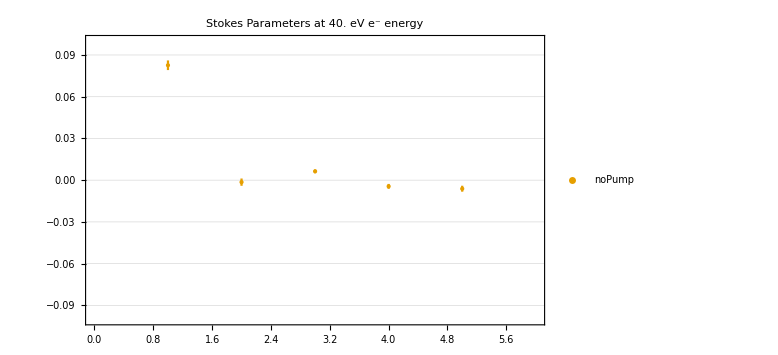
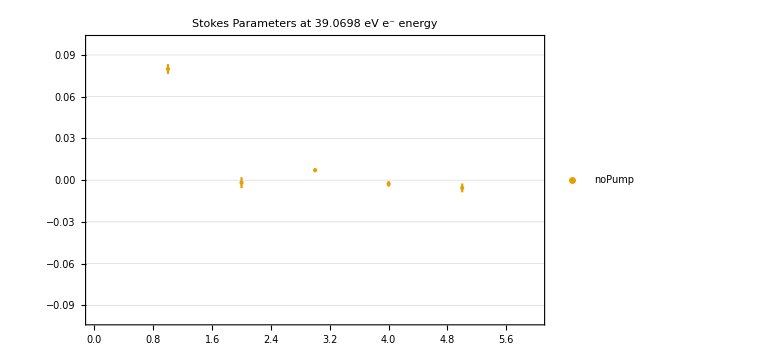
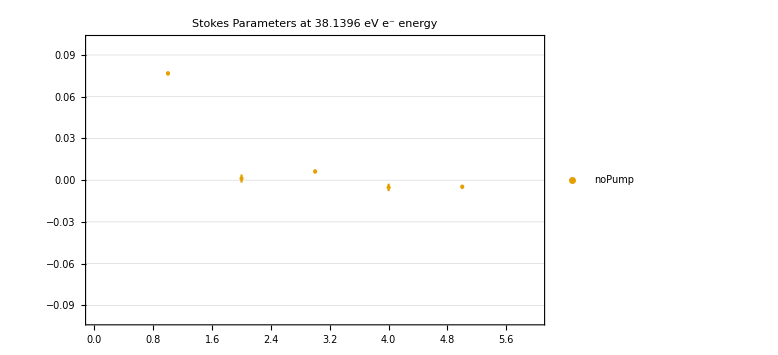
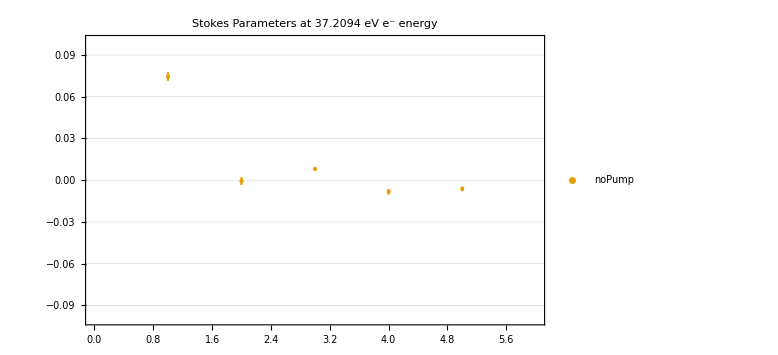
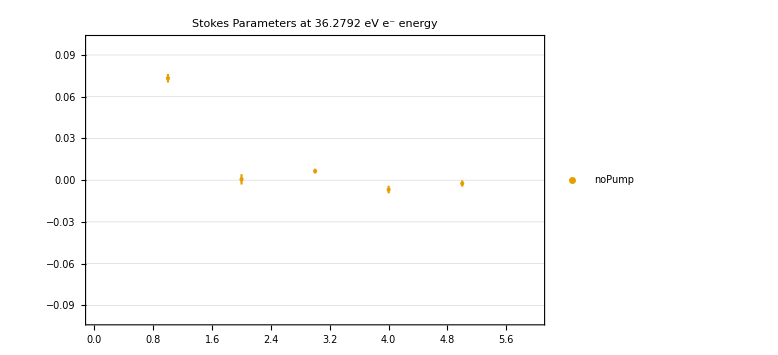
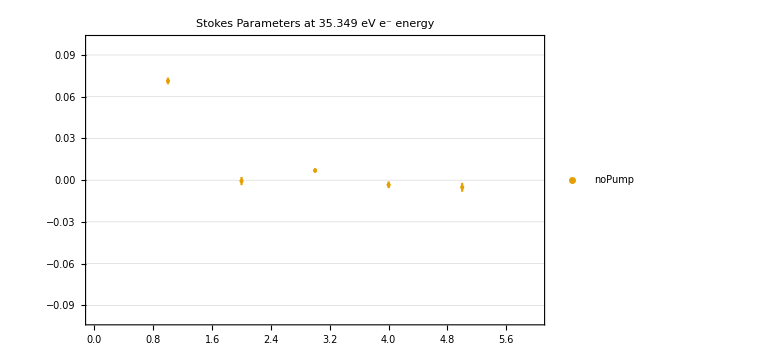
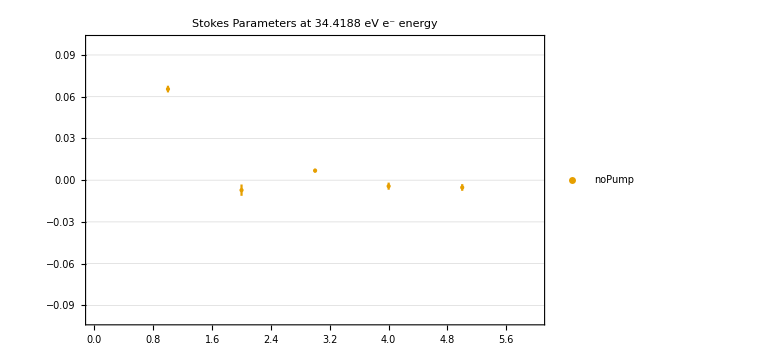
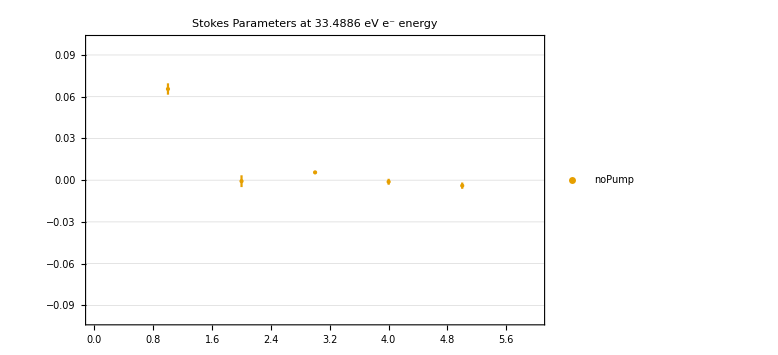
<|40.→-Graphics-,39.0698→-Graphics-,38.1396→-Graphics-,37.2094→-Graphics-,36.2792→-Graphics-,35.349→-Graphics-,34.4188→-Graphics-,33.4886→-Graphics-,32.5584→-Graphics-,31.6282→-Graphics-,30.698→-Graphics-,29.7678→-Graphics-,28.8376→-Graphics-,27.9073→-Graphics-,26.9771→-Graphics-,26.0469→-Graphics-,25.1167→-Graphics-,24.1865→-Graphics-,23.2563→-Graphics-,22.3261→-Graphics-,21.3959→-Graphics-,20.4657→-Graphics-|>

```mathematica
energyPlots=<||>;

energy=1;
pumpLight=1;
For[m=1,m≤Length[signalFiles[[1]]],m++,
plotData={};
plots={};
energyIndex=m;
For[i=1,i≤Length[allStokes[[energy]]],i++,
s=allStokes[[m]][[i]];
For[k=2,k≤Length[s[[1]]],k++,
AppendTo[plotData,{{k-1-.5((Length[stokes]-i)/Length[stokes]),s[[1]][[k]]},ErrorBar[s[[2]][[k]]]}];
];
height=.1;
AppendTo[plots,ErrorListPlot[Legended[plotData,Keys[stokes][[i]]],GridLines->Automatic,ImageSize->{960,600},AxesOrigin->{0,-height},PlotRange->{{0,6},{-height,height}},PlotStyle->colorBlindPallete[[i]],Ticks->{{{1,"P_1"},{2,"P_2"},{3,"|P_3|"},{4,"P_3:C2"},{5,"P_3:S2:"}},Automatic}]];
];
AppendTo[energyPlots,
Keys[signalFiles[[1]]][[m]]->Show[plots,ImageSize->Large,PlotLabel->"Stokes Parameters at "<>ToString[Keys[signalFiles[[1]]][[energyIndex]]]<>" eV e^- energy",Ticks->{{{1,"P_1"},{2,"P_2"},{3,"|P_3|"},{4,"P_3:C2"},{5,"P_3:S2:"}},Automatic}]
];

];
energyPlots
```

## Plot Individual Stokes Parameters as a Function of Electron Energy

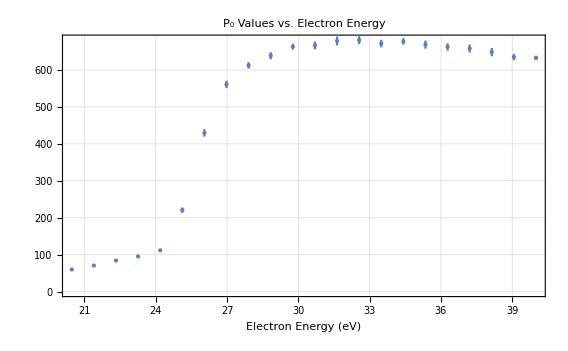
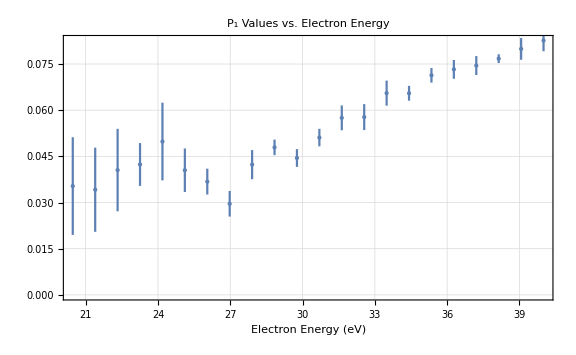
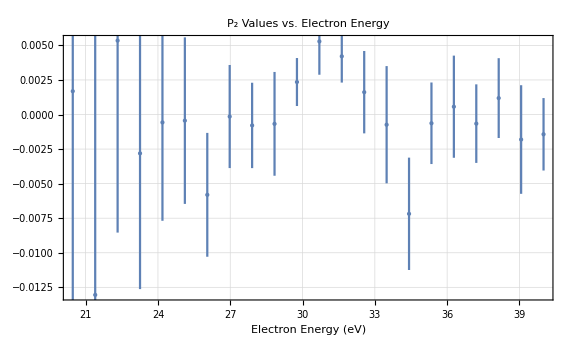
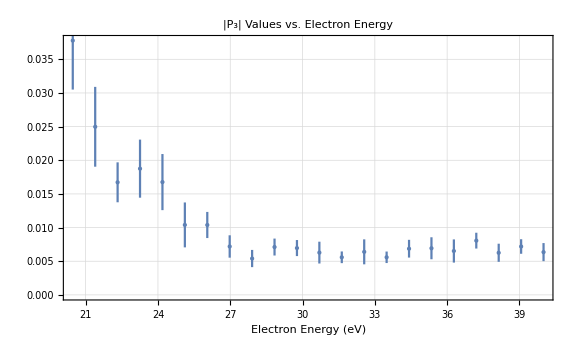
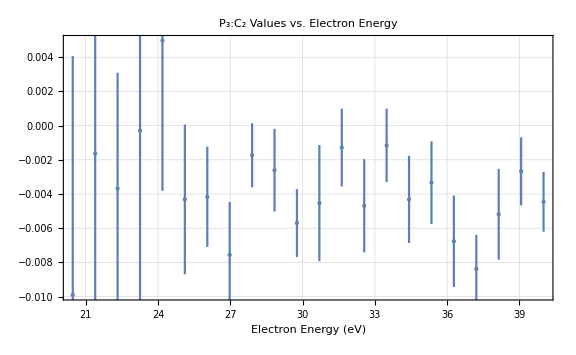
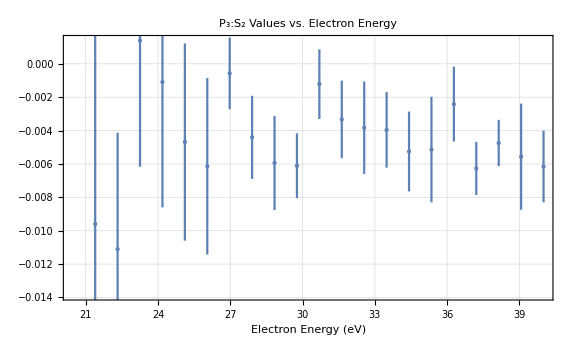
<|P_0→-Graphics-,P_1→-Graphics-,P_2→-Graphics-,|P_3|→-Graphics-,P_3:C_2→-Graphics-,P_3:S_2→-Graphics-|>

<|P_0→{{{40.,632.79},ErrorBar[5.82196]},{{39.0698,635.247},ErrorBar[8.55684]},{{38.1396,648.561},ErrorBar[11.2332]},{{37.2094,658.269},ErrorBar[11.0075]},{{36.2792,662.415},ErrorBar[9.99238]},{{35.349,668.797},ErrorBar[10.988]},{{34.4188,677.514},ErrorBar[8.83562]},{{33.4886,671.699},ErrorBar[10.1912]},{{32.5584,680.938},ErrorBar[10.4815]},{{31.6282,678.661},ErrorBar[11.83]},{{30.698,666.636},ErrorBar[10.6572]},{{29.7678,663.009},ErrorBar[8.07251]},{{28.8376,638.712},ErrorBar[9.53229]},{{27.9073,612.472},ErrorBar[8.63335]},{{26.9771,561.084},ErrorBar[10.0613]},{{26.0469,429.764},ErrorBar[10.0778]},{{25.1167,220.461},ErrorBar[7.1926]},{{24.1865,111.713},ErrorBar[3.48531]},{{23.2563,95.174},ErrorBar[2.78069]},{{22.3261,83.9908},ErrorBar[2.07373]},{{21.3959,70.3924},ErrorBar[1.54223]},{{20.4657,59.7788},ErrorBar[1.1258]}},P_1→{{{40.,0.0826091},ErrorBar[0.0034624]},{{39.0698,0.0799041},ErrorBar[0.0035228]},{{38.1396,0.0767422},ErrorBar[0.00142093]},{{37.2094,0.0744909},ErrorBar[0.00307625]},{{36.2792,0.0732599},ErrorBar[0.0030445]},{{35.349,0.0713277},ErrorBar[0.00237199]},{{34.4188,0.0654894},ErrorBar[0.00240184]},{{33.4886,0.0655416},ErrorBar[0.00407372]},{{32.5584,0.057754},ErrorBar[0.00421127]},{{31.6282,0.0575079},ErrorBar[0.00403513]},{{30.698,0.0510996},ErrorBar[0.00284171]},{{29.7678,0.0444712},ErrorBar[0.00288426]},{{28.8376,0.0479118},ErrorBar[0.00253027]},{{27.9073,0.0423081},ErrorBar[0.0047315]},{{26.9771,0.0295964},ErrorBar[0.00415198]},{{26.0469,0.0368056},ErrorBar[0.00419405]},{{25.1167,0.0404875},ErrorBar[0.00707243]},{{24.1865,0.0498243},ErrorBar[0.0126214]},{{23.2563,0.0423597},ErrorBar[0.00695498]},{{22.3261,0.0405479},ErrorBar[0.0133979]},{{21.3959,0.0341624},ErrorBar[0.0136659]},{{20.4657,0.0353505},ErrorBar[0.0158614]}},P_2→{{{40.,-0.00143099},ErrorBar[0.00262005]},{{39.0698,-0.00180926},ErrorBar[0.0039277]},{{38.1396,0.0011877},ErrorBar[0.0028865]},{{37.2094,-0.000659443},ErrorBar[0.0028409]},{{36.2792,0.000565298},ErrorBar[0.00369437]},{{35.349,-0.000633192},ErrorBar[0.00294926]},{{34.4188,-0.00718262},ErrorBar[0.00406296]},{{33.4886,-0.000737837},ErrorBar[0.00423974]},{{32.5584,0.00161526},ErrorBar[0.00297952]},{{31.6282,0.00420807},ErrorBar[0.00189862]},{{30.698,0.00528666},ErrorBar[0.00240937]},{{29.7678,0.00235003},ErrorBar[0.00173551]},{{28.8376,-0.000675373},ErrorBar[0.0037534]},{{27.9073,-0.000789476},ErrorBar[0.00308788]},{{26.9771,-0.000145913},ErrorBar[0.00372794]},{{26.0469,-0.00580894},ErrorBar[0.00447892]},{{25.1167,-0.0004423},ErrorBar[0.00602285]},{{24.1865,-0.000571814},ErrorBar[0.00711588]},{{23.2563,-0.00281022},ErrorBar[0.00981776]},{{22.3261,0.0053472},ErrorBar[0.0138879]},{{21.3959,-0.0130471},ErrorBar[0.0192674]},{{20.4657,0.00168544},ErrorBar[0.0204965]}},|P_3|→{{{40.,0.0063537},ErrorBar[0.00134352]},{{39.0698,0.00718887},ErrorBar[0.00107982]},{{38.1396,0.00625837},ErrorBar[0.00134433]},{{37.2094,0.00805888},ErrorBar[0.00117367]},{{36.2792,0.00651992},ErrorBar[0.00172119]},{{35.349,0.00692672},ErrorBar[0.00163332]},{{34.4188,0.00686134},ErrorBar[0.00131836]},{{33.4886,0.00558547},ErrorBar[0.000853935]},{{32.5584,0.00639544},ErrorBar[0.00185446]},{{31.6282,0.00558405},ErrorBar[0.000866958]},{{30.698,0.00628196},ErrorBar[0.00162014]},{{29.7678,0.00695744},ErrorBar[0.00119215]},{{28.8376,0.00710768},ErrorBar[0.00125772]},{{27.9073,0.00540255},ErrorBar[0.00127823]},{{26.9771,0.00719193},ErrorBar[0.00166143]},{{26.0469,0.0103849},ErrorBar[0.0019401]},{{25.1167,0.0103955},ErrorBar[0.00333597]},{{24.1865,0.0167579},ErrorBar[0.0041668]},{{23.2563,0.0187544},ErrorBar[0.0043134]},{{22.3261,0.0167247},ErrorBar[0.00296646]},{{21.3959,0.0249745},ErrorBar[0.00592875]},{{20.4657,0.0377804},ErrorBar[0.00727755]}},P_3:C_2→{{{40.,-0.00445351},ErrorBar[0.00174879]},{{39.0698,-0.00267663},ErrorBar[0.00198981]},{{38.1396,-0.00518896},ErrorBar[0.00265492]},{{37.2094,-0.00838067},ErrorBar[0.00199212]},{{36.2792,-0.00676096},ErrorBar[0.00267444]},{{35.349,-0.00333481},ErrorBar[0.00241817]},{{34.4188,-0.00431399},ErrorBar[0.00254795]},{{33.4886,-0.00115733},ErrorBar[0.00214758]},{{32.5584,-0.00468719},ErrorBar[0.00272841]},{{31.6282,-0.00128496},ErrorBar[0.00227422]},{{30.698,-0.00453141},ErrorBar[0.00339641]},{{29.7678,-0.00570075},ErrorBar[0.00198538]},{{28.8376,-0.0026093},ErrorBar[0.00241626]},{{27.9073,-0.00173631},ErrorBar[0.00187881]},{{26.9771,-0.00756272},ErrorBar[0.00309714]},{{26.0469,-0.0041638},ErrorBar[0.00292705]},{{25.1167,-0.00431593},ErrorBar[0.00437447]},{{24.1865,0.00497318},ErrorBar[0.00878564]},{{23.2563,-0.000287874},ErrorBar[0.0104865]},{{22.3261,-0.00368159},ErrorBar[0.00677597]},{{21.3959,-0.00162903},ErrorBar[0.0116153]},{{20.4657,-0.00990038},ErrorBar[0.0139667]}},P_3:S_2→{{{40.,-0.00615033},ErrorBar[0.00214645]},{{39.0698,-0.00556333},ErrorBar[0.00317802]},{{38.1396,-0.00474356},ErrorBar[0.00138926]},{{37.2094,-0.00626799},ErrorBar[0.00159384]},{{36.2792,-0.00241404},ErrorBar[0.00224407]},{{35.349,-0.00513659},ErrorBar[0.00316565]},{{34.4188,-0.00525215},ErrorBar[0.00239086]},{{33.4886,-0.0039586},ErrorBar[0.00225912]},{{32.5584,-0.00382756},ErrorBar[0.00277246]},{{31.6282,-0.00333086},ErrorBar[0.00232304]},{{30.698,-0.00121736},ErrorBar[0.0020864]},{{29.7678,-0.0061043},ErrorBar[0.00194045]},{{28.8376,-0.00593851},ErrorBar[0.00282011]},{{27.9073,-0.00440431},ErrorBar[0.002488]},{{26.9771,-0.000572707},ErrorBar[0.00214561]},{{26.0469,-0.00614049},ErrorBar[0.00528478]},{{25.1167,-0.00468635},ErrorBar[0.00590731]},{{24.1865,-0.00109141},ErrorBar[0.00751031]},{{23.2563,0.00139201},ErrorBar[0.00756239]},{{22.3261,-0.0111047},ErrorBar[0.00697826]},{{21.3959,-0.0095973},ErrorBar[0.0120985]},{{20.4657,-0.0321868},ErrorBar[0.0148777]}}|>

stokesPlots.png

```mathematica
plotLabels={"P_0","P_1","P_2","|P_3|","P_3:C_2","P_3:S_2"};
energy=1;
pumpLight=1;
valueOrError=1;

plotData=<||>;
plots=<||>;

For[stokesIndex=1,stokesIndex≤ Length[plotLabels],stokesIndex++,
plotPoints={};
For[energy=1,energy≤Length[allStokes],energy++,
plotPoint={{Keys[allStokes][[energy]],allStokes[[energy]][[pumpLight]][[1]][stokesNames[[stokesIndex]]]},ErrorBar[allStokes[[energy]][[pumpLight]][[2]][stokesErrNames[[stokesIndex]]]]};
AppendTo[plotPoints,plotPoint];
];
AppendTo[plotData,plotLabels[[stokesIndex]]->plotPoints];
AppendTo[plots,plotLabels[[stokesIndex]]->
ErrorListPlot[plotPoints,PlotRange->{Automatic,Automatic},GridLines->Automatic,Frame->True,PlotLabel->  plotLabels[[stokesIndex]]<> " Values vs. Electron Energy",FrameLabel->{"Electron Energy (eV)",None}]]
];
plots
plotData
Export["stokesPlots.png",plots,ImageResolution->200]
```

## Display all raw data and averages

Pump Light: noPump, Energy: 40.

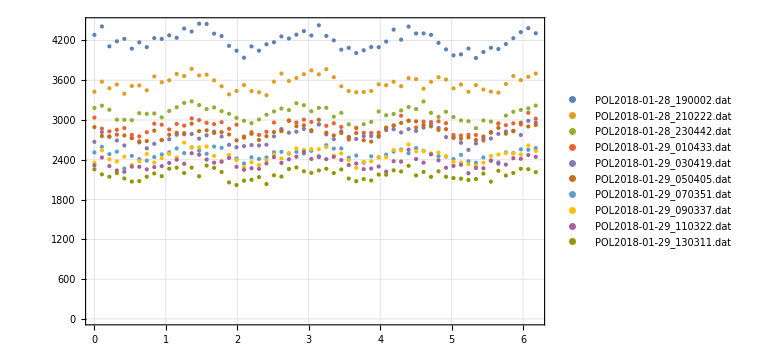

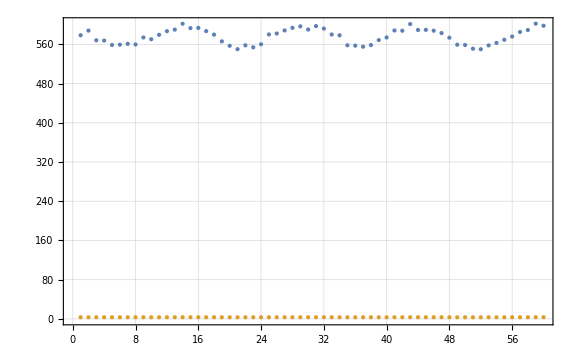

Pump Light: noPump, Energy: 39.0698

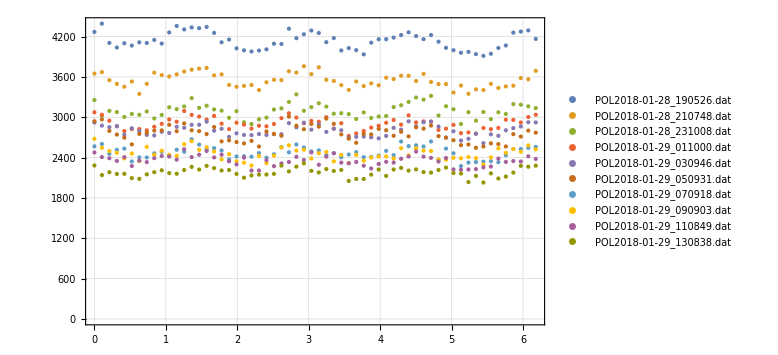

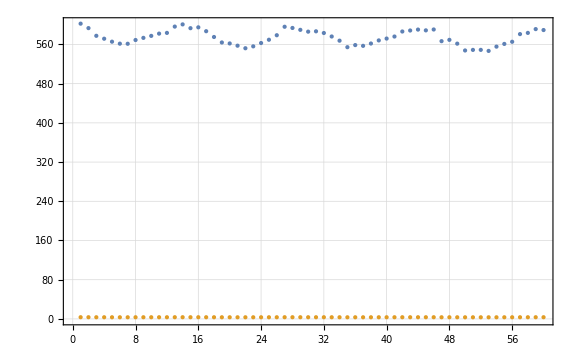

Pump Light: noPump, Energy: 38.1396

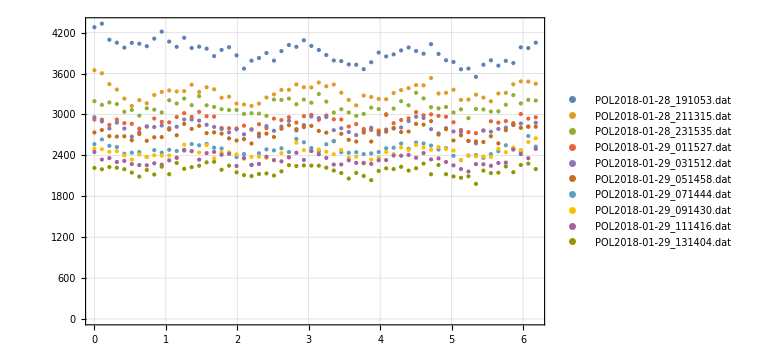

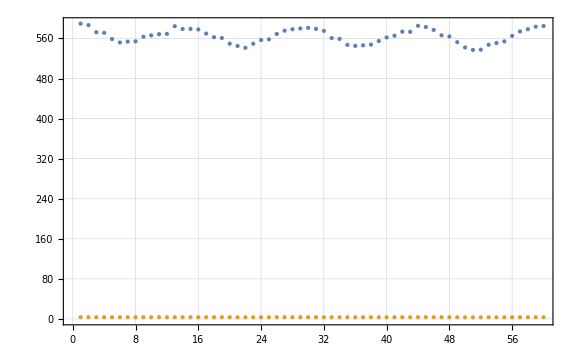

Pump Light: noPump, Energy: 37.2094

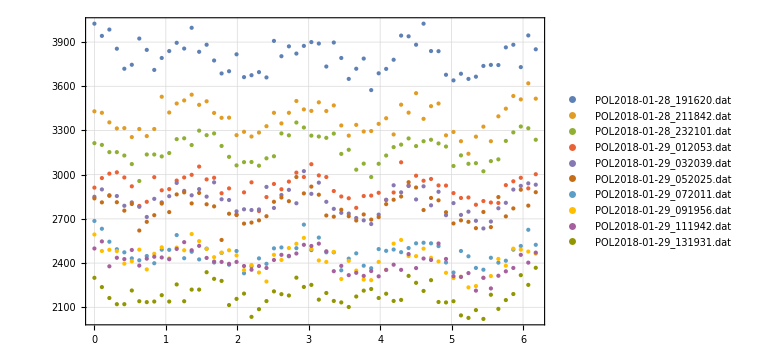

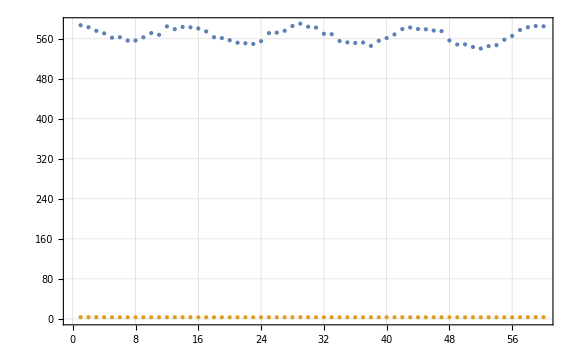

Pump Light: noPump, Energy: 36.2792

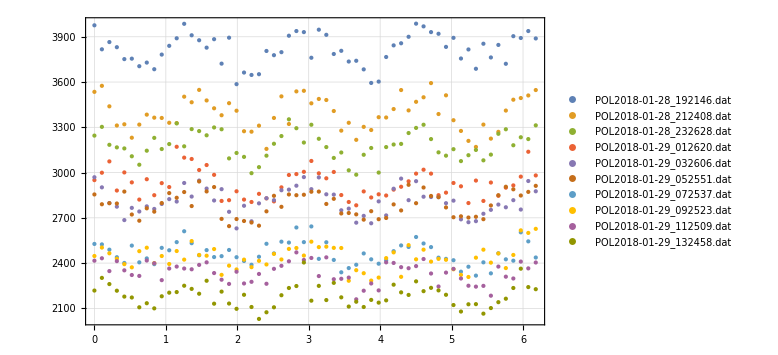

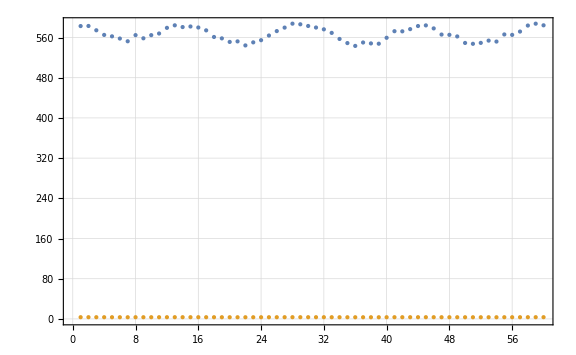

Pump Light: noPump, Energy: 35.349

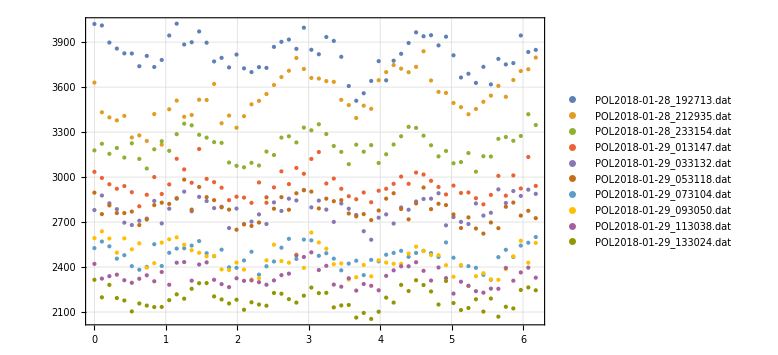

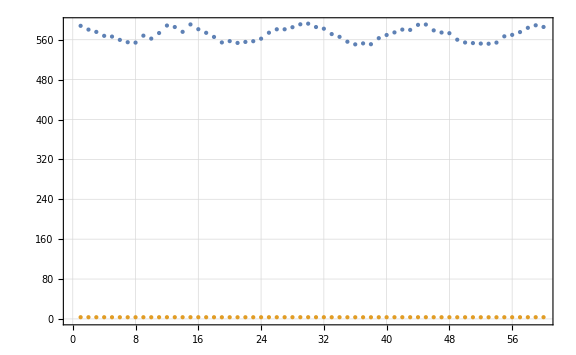

Pump Light: noPump, Energy: 34.4188

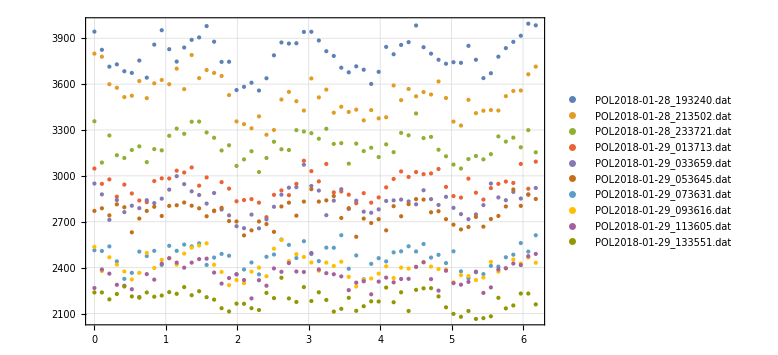

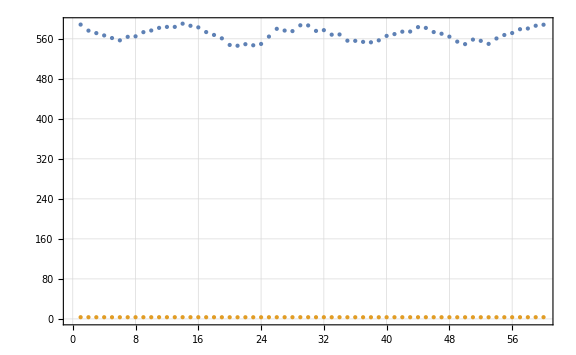

Pump Light: noPump, Energy: 33.4886

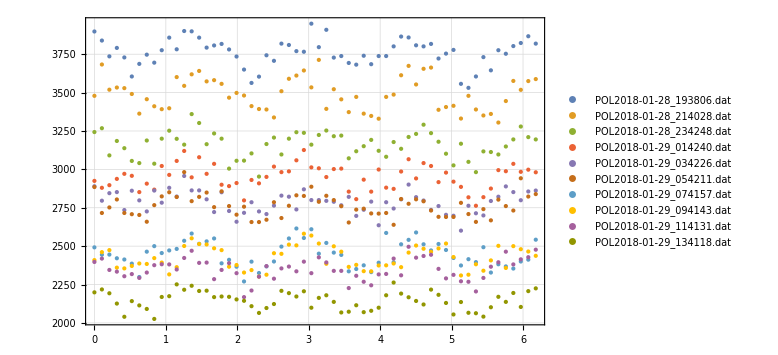

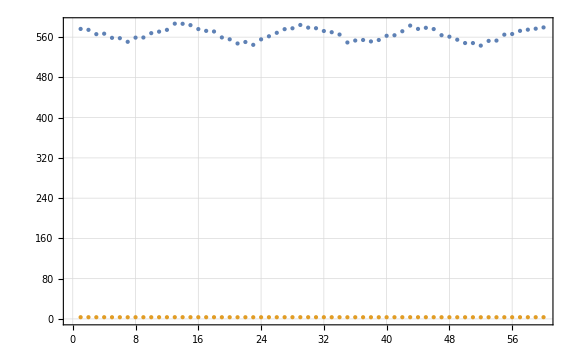

Pump Light: noPump, Energy: 32.5584

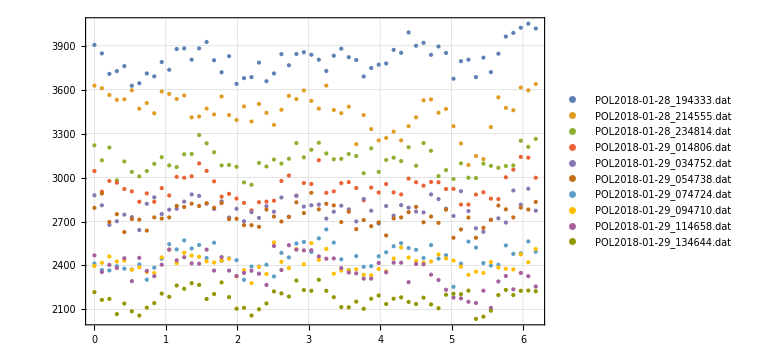

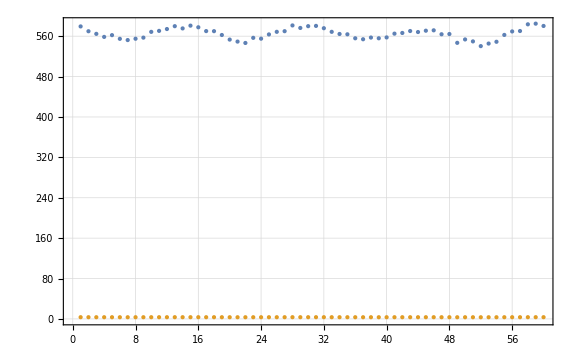

Pump Light: noPump, Energy: 31.6282

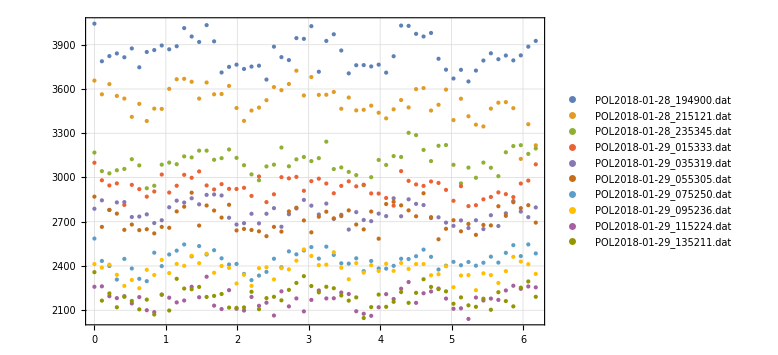

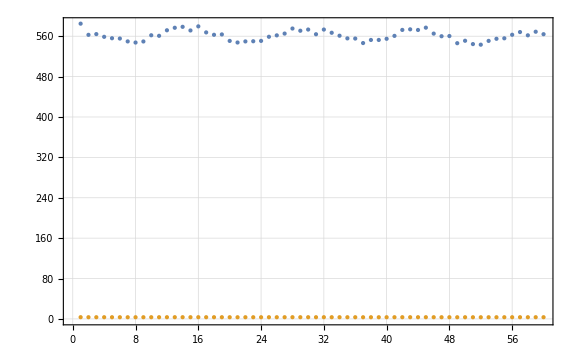

Pump Light: noPump, Energy: 30.698

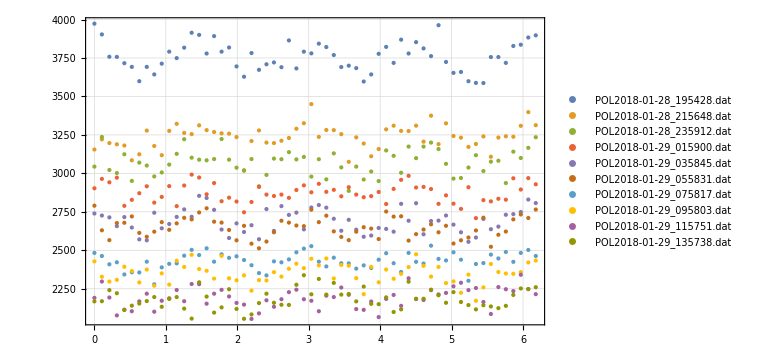

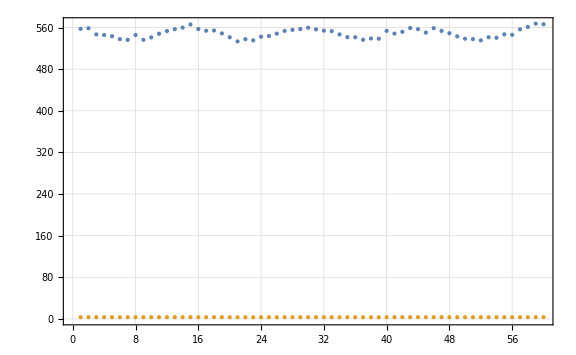

Pump Light: noPump, Energy: 29.7678

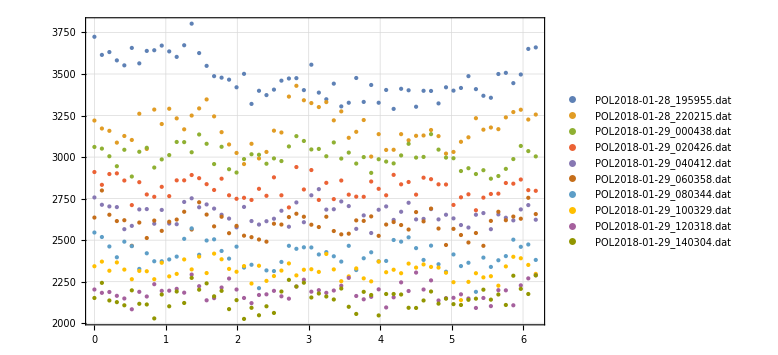

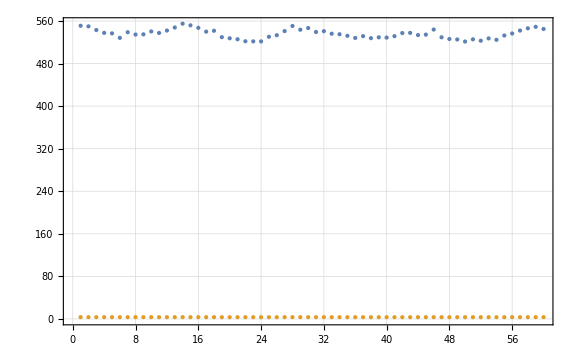

Pump Light: noPump, Energy: 28.8376

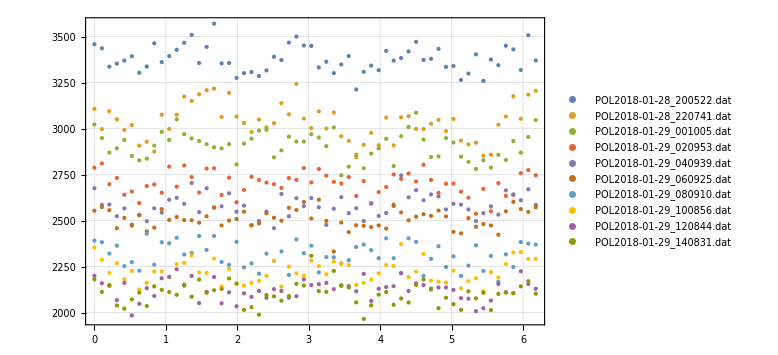

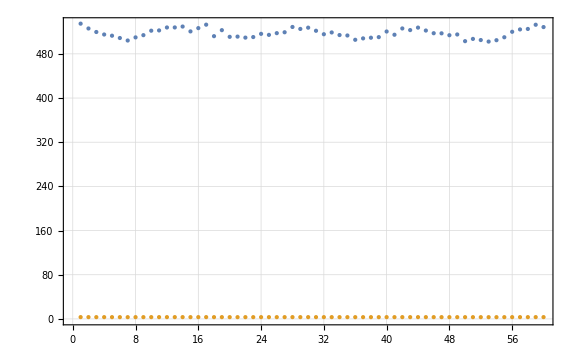

Pump Light: noPump, Energy: 27.9073

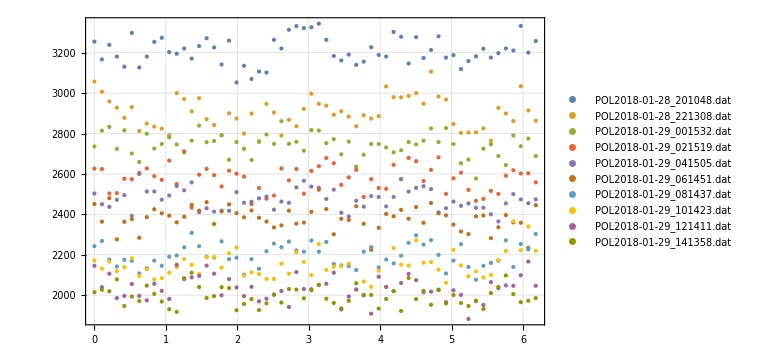

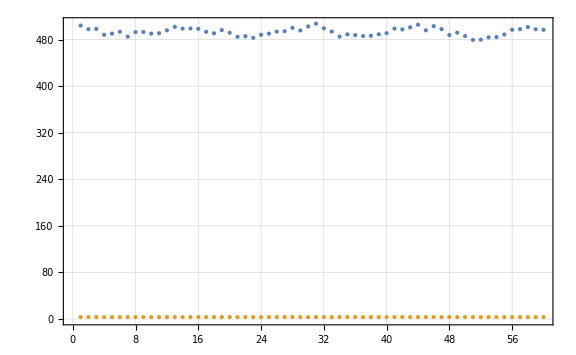

Pump Light: noPump, Energy: 26.9771

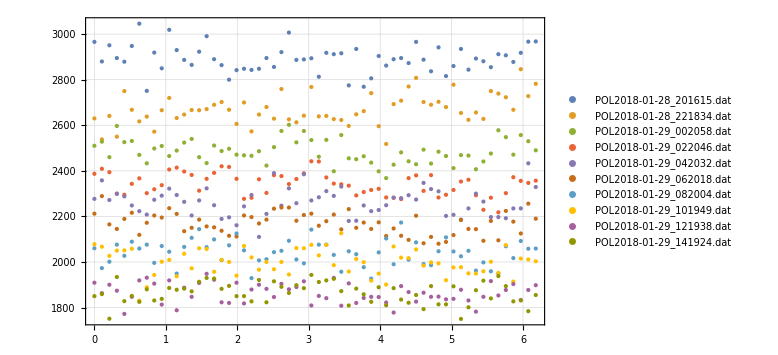

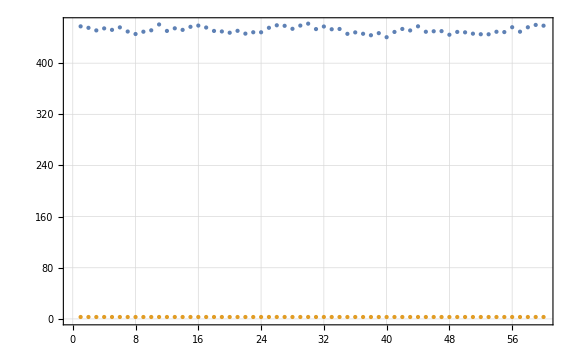

Pump Light: noPump, Energy: 26.0469

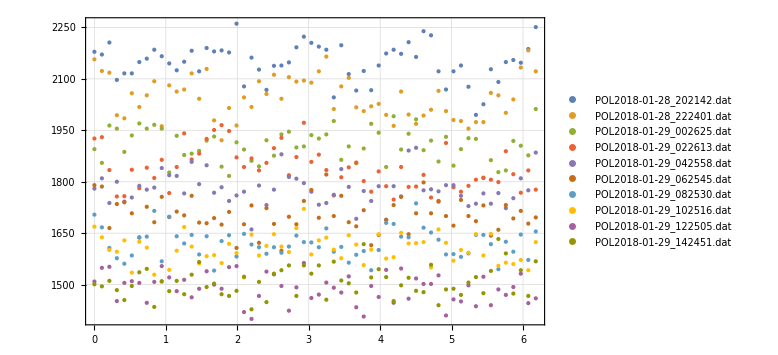

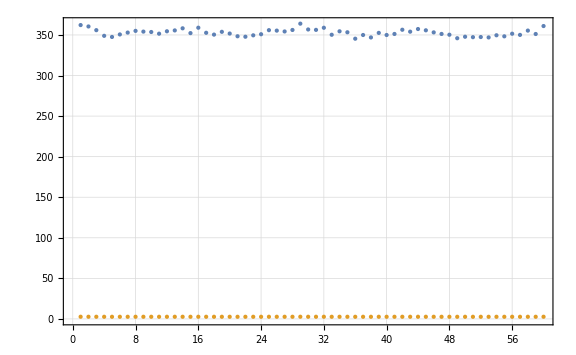

Pump Light: noPump, Energy: 25.1167

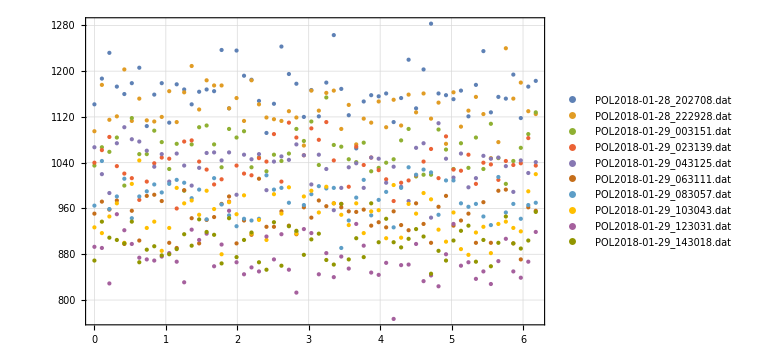

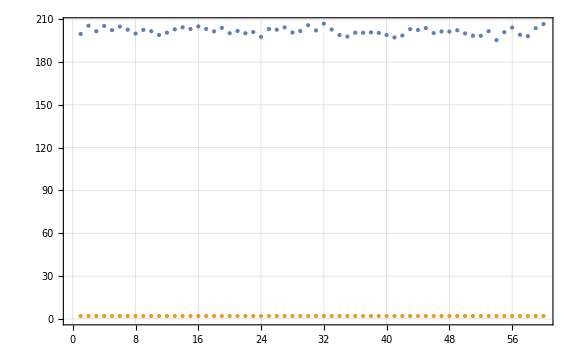

Pump Light: noPump, Energy: 24.1865

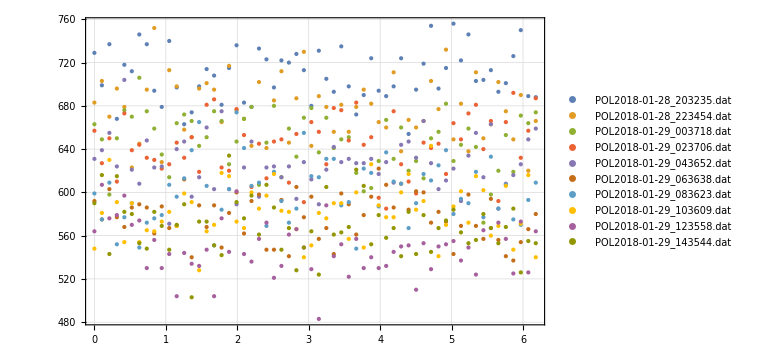

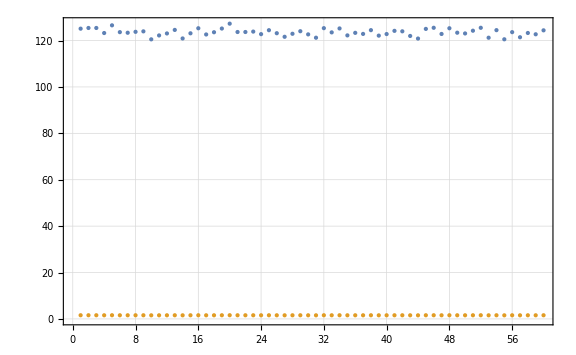

Pump Light: noPump, Energy: 23.2563

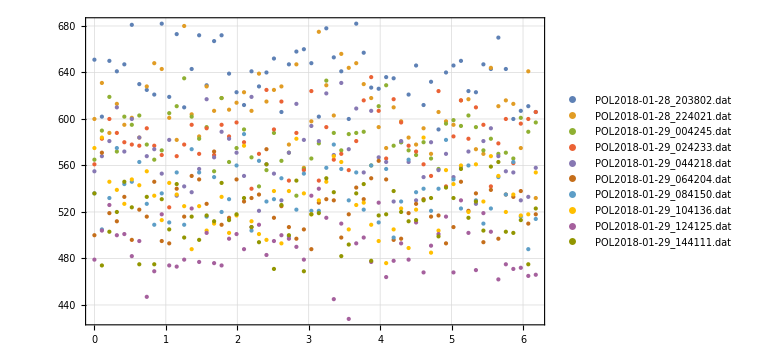

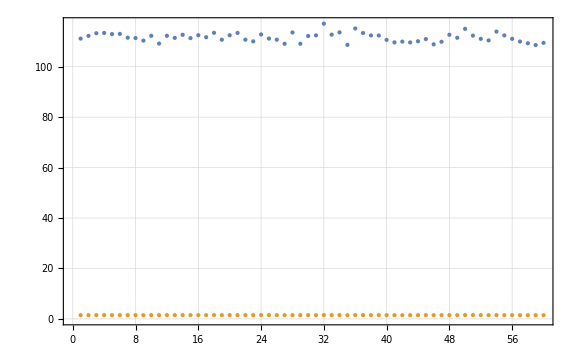

Pump Light: noPump, Energy: 22.3261

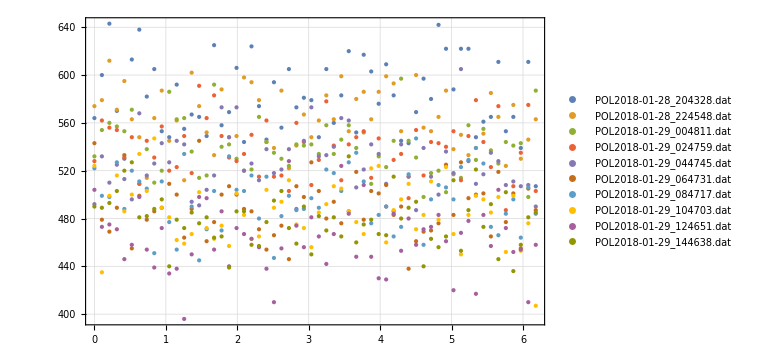

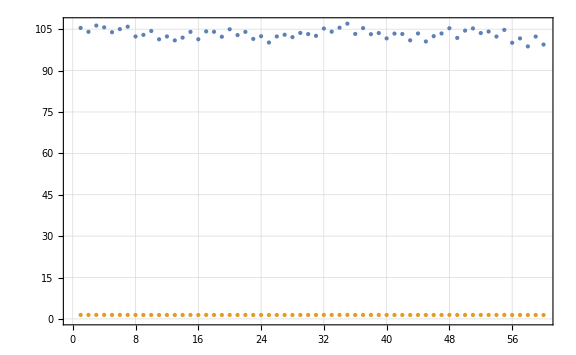

Pump Light: noPump, Energy: 21.3959

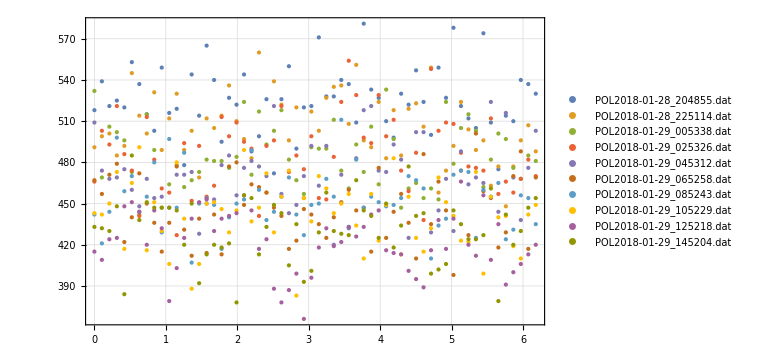

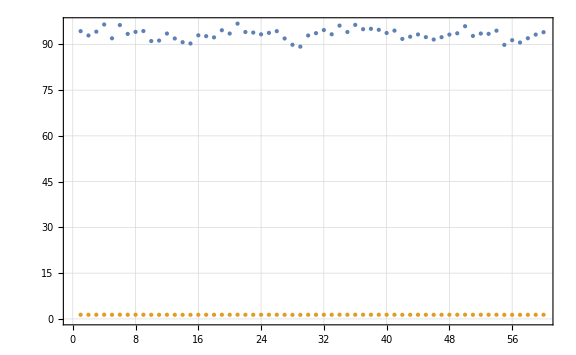

Pump Light: noPump, Energy: 20.4657

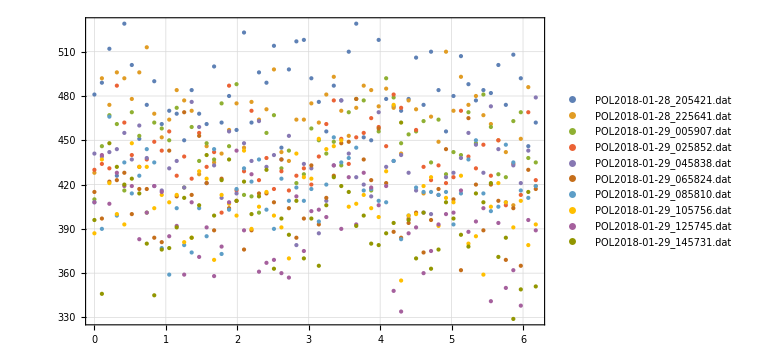

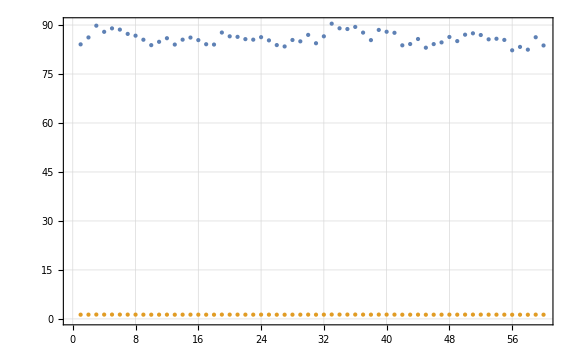

```mathematica
allStokes=<||>;
stokes=<||>;
allFiles=signalFiles;
For[j=1,j<=Length[allFiles],j++,
For[i=1,i<=Length[allFiles[[j]]],i++,
Print["Pump Light: "<>ToString[Keys[allFiles][[j]]]<>", Energy: "<>ToString[Keys[allFiles[[j]]][[i]]]]; 
Print[PlotListOfPolFileNames[allFiles[[j]][[i]]]];
Print[ListPlot[GetAverageCountRateFromFileNames[allFiles[[j]][[i]]]]];
AppendTo[stokes,Keys[allFiles[[j]]][[i]]->GetStokesFromFileNames[allFiles[[j]][[i]]]]
];
AppendTo[allStokes,Keys[allFiles][[j]]->stokes]
];
```

## Show representative Background Subtraction

20.5

-Graphics-

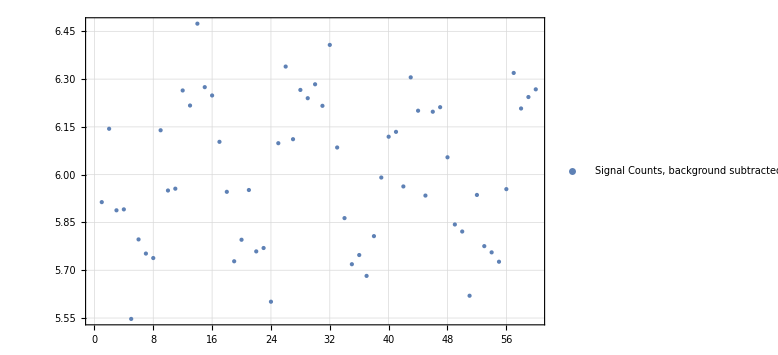

{{{0.,0.0196897,0.0107138,-0.00687267,-0.194024,0.00246389,-0.0245766,-0.031025,0.00916748,-0.0313869,0.0466559,-0.00744179,0.0370965,0.0300348,-0.0283526,-0.0061078,0.028802,-0.0219889,-0.0130036,-0.0138919,0.0111619,-0.0472431,-0.0117102,0.0300615,0.0190524,0.0397025,0.0192608,-0.00184946,0.00251341,-0.00145248},{}},{{6.00509,-0.037192,-0.00295402,-0.033574,0.17991,0.0130805,0.0211375,-0.0334832,0.0127896,0.0175454,-0.0260362,-0.0528276,0.00364163,-0.0119428,0.0265095,0.0157344,-0.0311305,0.021145,-0.0404522,-0.0290924,-0.00887327,0.0100153,0.00702558,-0.0132755,-0.00230303,-0.0261402,-0.042568,0.0249345,-0.0150553,-0.00805061},{}}}

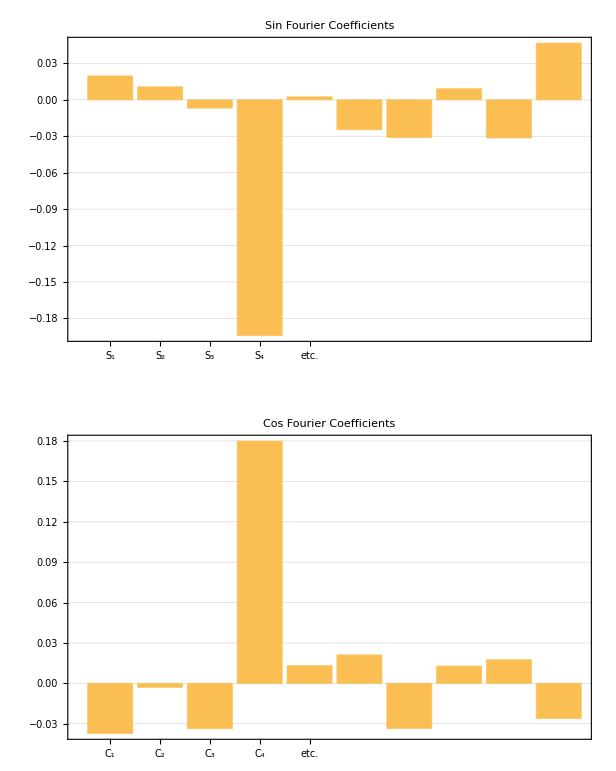

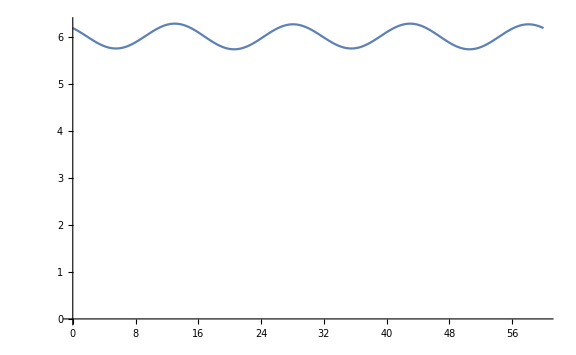

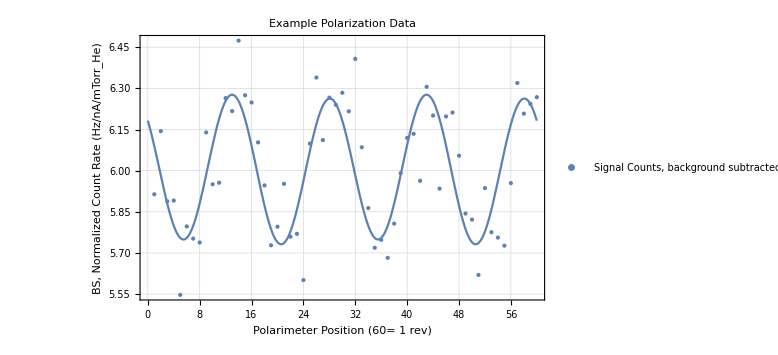

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-01-28_hayesReproduction\analysis

samplePolarization.png

sampleFC.png

backGroundSubtractionSample.png

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-01-28_hayesReproduction\data

-Graphics-

{{{0.,0.0196897,0.0107138,-0.00687267,-0.194024,0.00246389,-0.0245766,-0.031025,0.00916748,-0.0313869,0.0466559,-0.00744179,0.0370965,0.0300348,-0.0283526,-0.0061078,0.028802,-0.0219889,-0.0130036,-0.0138919,0.0111619,-0.0472431,-0.0117102,0.0300615,0.0190524,0.0397025,0.0192608,-0.00184946,0.00251341,-0.00145248},{}},{{6.00509,-0.037192,-0.00295402,-0.033574,0.17991,0.0130805,0.0211375,-0.0334832,0.0127896,0.0175454,-0.0260362,-0.0528276,0.00364163,-0.0119428,0.0265095,0.0157344,-0.0311305,0.021145,-0.0404522,-0.0290924,-0.00887327,0.0100153,0.00702558,-0.0132755,-0.00230303,-0.0261402,-0.042568,0.0249345,-0.0150553,-0.00805061},{}}}

-Graphics-

-Graphics-

-Graphics-

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-01-28_hayesReproduction\analysis

samplePolarization.png

sampleS2.png

sampleC2.png

backGroundSubtractionSample.png

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-01-28_hayesReproduction\data

-Graphics-

{{{0.,0.0196897,0.0107138,-0.00687267,-0.194024,0.00246389,-0.0245766,-0.031025,0.00916748,-0.0313869,0.0466559,-0.00744179,0.0370965,0.0300348,-0.0283526,-0.0061078,0.028802,-0.0219889,-0.0130036,-0.0138919,0.0111619,-0.0472431,-0.0117102,0.0300615,0.0190524,0.0397025,0.0192608,-0.00184946,0.00251341,-0.00145248},{}},{{6.00509,-0.037192,-0.00295402,-0.033574,0.17991,0.0130805,0.0211375,-0.0334832,0.0127896,0.0175454,-0.0260362,-0.0528276,0.00364163,-0.0119428,0.0265095,0.0157344,-0.0311305,0.021145,-0.0404522,-0.0290924,-0.00887327,0.0100153,0.00702558,-0.0132755,-0.00230303,-0.0261402,-0.042568,0.0249345,-0.0150553,-0.00805061},{}}}

-Graphics-

-Graphics-

-Graphics-

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-01-28_hayesReproduction\analysis

samplePolarization.png

sampleS2.png

sampleC2.png

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-01-28_hayesReproduction\data

-Graphics-

{{{0.,0.0196897,0.0107138,-0.00687267,-0.194024,0.00246389,-0.0245766,-0.031025,0.00916748,-0.0313869,0.0466559,-0.00744179,0.0370965,0.0300348,-0.0283526,-0.0061078,0.028802,-0.0219889,-0.0130036,-0.0138919,0.0111619,-0.0472431,-0.0117102,0.0300615,0.0190524,0.0397025,0.0192608,-0.00184946,0.00251341,-0.00145248},{}},{{6.00509,-0.037192,-0.00295402,-0.033574,0.17991,0.0130805,0.0211375,-0.0334832,0.0127896,0.0175454,-0.0260362,-0.0528276,0.00364163,-0.0119428,0.0265095,0.0157344,-0.0311305,0.021145,-0.0404522,-0.0290924,-0.00887327,0.0100153,0.00702558,-0.0132755,-0.00230303,-0.0261402,-0.042568,0.0249345,-0.0150553,-0.00805061},{}}}

-Graphics-

-Graphics-

-Graphics-

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-01-28_hayesReproduction\analysis

samplePolarization.png

sampleS2.png

sampleC2.png

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-01-28_hayesReproduction\data

-Graphics-

{{{0.,0.0196897,0.0107138,-0.00687267,-0.194024,0.00246389,-0.0245766,-0.031025,0.00916748,-0.0313869,0.0466559,-0.00744179,0.0370965,0.0300348,-0.0283526,-0.0061078,0.028802,-0.0219889,-0.0130036,-0.0138919,0.0111619,-0.0472431,-0.0117102,0.0300615,0.0190524,0.0397025,0.0192608,-0.00184946,0.00251341,-0.00145248},{}},{{6.00509,-0.037192,-0.00295402,-0.033574,0.17991,0.0130805,0.0211375,-0.0334832,0.0127896,0.0175454,-0.0260362,-0.0528276,0.00364163,-0.0119428,0.0265095,0.0157344,-0.0311305,0.021145,-0.0404522,-0.0290924,-0.00887327,0.0100153,0.00702558,-0.0132755,-0.00230303,-0.0261402,-0.042568,0.0249345,-0.0150553,-0.00805061},{}}}

-Graphics-

-Graphics-

-Graphics-

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-01-28_hayesReproduction\analysis

samplePolarization.png

sampleS2.png

sampleC2.png

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-01-28_hayesReproduction\data

-Graphics-

{{{0.,0.0196897,0.0107138,-0.00687267,-0.194024,0.00246389,-0.0245766,-0.031025,0.00916748,-0.0313869,0.0466559,-0.00744179,0.0370965,0.0300348,-0.0283526,-0.0061078,0.028802,-0.0219889,-0.0130036,-0.0138919,0.0111619,-0.0472431,-0.0117102,0.0300615,0.0190524,0.0397025,0.0192608,-0.00184946,0.00251341,-0.00145248},{}},{{6.00509,-0.037192,-0.00295402,-0.033574,0.17991,0.0130805,0.0211375,-0.0334832,0.0127896,0.0175454,-0.0260362,-0.0528276,0.00364163,-0.0119428,0.0265095,0.0157344,-0.0311305,0.021145,-0.0404522,-0.0290924,-0.00887327,0.0100153,0.00702558,-0.0132755,-0.00230303,-0.0261402,-0.042568,0.0249345,-0.0150553,-0.00805061},{}}}

-Graphics-

-Graphics-

-Graphics-

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-01-28_hayesReproduction\analysis

samplePolarization.png

sampleS2.png

sampleC2.png

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-01-28_hayesReproduction\data

-Graphics-

{{{0.,0.0196897,0.0107138,-0.00687267,-0.194024,0.00246389,-0.0245766,-0.031025,0.00916748,-0.0313869,0.0466559,-0.00744179,0.0370965,0.0300348,-0.0283526,-0.0061078,0.028802,-0.0219889,-0.0130036,-0.0138919,0.0111619,-0.0472431,-0.0117102,0.0300615,0.0190524,0.0397025,0.0192608,-0.00184946,0.00251341,-0.00145248},{}},{{6.00509,-0.037192,-0.00295402,-0.033574,0.17991,0.0130805,0.0211375,-0.0334832,0.0127896,0.0175454,-0.0260362,-0.0528276,0.00364163,-0.0119428,0.0265095,0.0157344,-0.0311305,0.021145,-0.0404522,-0.0290924,-0.00887327,0.0100153,0.00702558,-0.0132755,-0.00230303,-0.0261402,-0.042568,0.0249345,-0.0150553,-0.00805061},{}}}

-Graphics-

-Graphics-

-Graphics-

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-01-28_hayesReproduction\analysis

samplePolarization.png

sampleS2.png

sampleC2.png

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-01-28_hayesReproduction\data

-Graphics-

{{{0.,0.0196897,0.0107138,-0.00687267,-0.194024,0.00246389,-0.0245766,-0.031025,0.00916748,-0.0313869,0.0466559,-0.00744179,0.0370965,0.0300348,-0.0283526,-0.0061078,0.028802,-0.0219889,-0.0130036,-0.0138919,0.0111619,-0.0472431,-0.0117102,0.0300615,0.0190524,0.0397025,0.0192608,-0.00184946,0.00251341,-0.00145248},{}},{{6.00509,-0.037192,-0.00295402,-0.033574,0.17991,0.0130805,0.0211375,-0.0334832,0.0127896,0.0175454,-0.0260362,-0.0528276,0.00364163,-0.0119428,0.0265095,0.0157344,-0.0311305,0.021145,-0.0404522,-0.0290924,-0.00887327,0.0100153,0.00702558,-0.0132755,-0.00230303,-0.0261402,-0.042568,0.0249345,-0.0150553,-0.00805061},{}}}

-Graphics-

-Graphics-

-Graphics-

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-01-28_hayesReproduction\analysis

samplePolarization.png

sampleS2.png

sampleC2.png

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-01-28_hayesReproduction\data

```mathematica
pumpStyle=1;
energy=1;
runNumber=2;
xAxisLabel="Retarder Position (60=1 Rev)";
imageRes=100;



averageDarkCounts=GetAverageCountRateFromFileNames[darkFiles[[pumpStyle]][[energy]]];


molyFile=ImportFile[molyFiles[[pumpStyle]][[energy]][[runNumber]]];
dwell=molyFile[[1]]["#DWELL(s):"];
currentScale=molyFile[[1]]["#SCALE:"];

countRateData=Normal[molyFile[[2]][[All,"COUNT"]]]/dwell;
currentData=Abs[Normal[molyFile[[2]][[All,"CURRENT"]]]*10^(-currentScale)/nA];


molyMinusDark=countRateData-averageDarkCounts[[1]];
molyMinusDarkPlot=ListPlot[{Legended[averageDarkCounts[[1]],"Dark Counts\n(4 run average)"],Legended[countRateData,"Representative\nMoly Count Rate"],Legended[molyMinusDark,"Moly Minus Dark"]},PlotLabel->"Moly Count Dark Subtraction",FrameLabel->{xAxisLabel,"Count Rate"}];

molyCurrentPlot=ListPlot[currentData,PlotLabel->"Representative Moly Current",PlotRange->{Automatic,{Automatic,Automatic}},FrameLabel->{xAxisLabel,"Current (nA)"}];

molyMinusDarkCurrentNorm=molyMinusDark/currentData;
molyMinusDarkCurrentNormPlot=ListPlot[molyMinusDarkCurrentNorm,PlotLabel->"Moly Minus Dark, Current Normalized",FrameLabel->{xAxisLabel,"Count Rate, Current Normalized (Hz/nA)"}] ;


signalFile=ImportFile[signalFiles[[pumpStyle]][[energy]][[runNumber]]];
dwell=signalFile[[1]]["#DWELL(s):"];
currentScale=signalFile[[1]]["#SCALE:"];
mTorrHe=signalFile[[1]]["#CVGauge(He)(Torr):"]/mTorr;

countRateData=Normal[signalFile[[2]][[All,"COUNT"]]]/dwell;
currentData=Abs[Normal[signalFile[[2]][[All,"CURRENT"]]]*10^(-currentScale)/nA];
20.5

signalMinusDark=countRateData-averageDarkCounts[[1]];
signalMinusDarkPlot=ListPlot[{Legended[countRateData,"Raw Signal\nCounts"],Legended[signalMinusDark,"Raw Signal\nMinus Dark"]},PlotLabel->"Signal Minus Dark Counts",FrameLabel->{xAxisLabel,"Count Rate (Hz)"}];

signalCurrentPlot=ListPlot[currentData,PlotLabel->"Representative Signal Current",PlotRange->{Automatic,{Automatic,Automatic}},FrameLabel->{xAxisLabel,"Current (nA)"}];

signalMinusMoly=signalMinusDark/currentData-molyMinusDarkCurrentNorm ;
signalCurrentNormSubtractionPlot=ListPlot[{Legended[signalMinusDark/currentData,"Signal Minus Dark,\nCurrent Normalized"],Legended[molyMinusDarkCurrentNorm,"Moly Counts,\nCurrent Normalized"],Legended[signalMinusMoly,"Signal Minus Moly,\nCurrent Normalized"]},PlotLabel->"Signal Background Subtraction",FrameLabel->{xAxisLabel,"Count Rate, Current Normalized (Hz/nA)"}];

grid=GraphicsGrid[{{molyMinusDarkPlot,signalMinusDarkPlot},
{molyCurrentPlot,signalCurrentPlot},
{molyMinusDarkCurrentNormPlot,signalCurrentNormSubtractionPlot}},ImageSize->{1510,Automatic}]

signalMinusMolyHeNormalized=signalMinusMoly/mTorrHe;
finalPlot=ListPlot[Legended[signalMinusMolyHeNormalized,"Signal Counts, background subtracted,\n helium pressure normalized."]]
fc=DFT[signalMinusMolyHeNormalized]
sine=1;
cosine=2;
signal=1;
error=2;
sin=fc[[sine]][[signal]];
cos=fc[[cosine]][[signal]];
sinBar=BarChart[Take[sin,{2,11}],PlotLabel->"Sin Fourier Coefficients",ChartLabels->{"S_1","S_2","S_3","S_4","etc."},Frame->True];
cosBar=BarChart[Take[cos,{2,11}],PlotLabel->"Cos Fourier Coefficients",ChartLabels->{"C_1","C_2","C_3","C_4","etc."},Frame->True];
fcPlot=GraphicsGrid[{{sinBar},{cosBar}}]
recreation[θ_]:=cos[[1]]+cos[[3]]Cos[2(θ*π/30)]+sin[[3]]Sin[2(θ*π/30)]+cos[[5]]Cos[4(θ*π/30)]+sin[[5]]Sin[4(θ*π/30)];
simulation=Plot[recreation[θ],{θ,0,60},PlotRange->{Automatic,{0,Automatic}}]
samplePol=Show[{finalPlot,simulation},PlotRange->{Automatic,{0,Automatic}},PlotLabel->"Example Polarization Data",FrameLabel-> {"Polarimeter Position (60= 1 rev)","BS, Normalized Count Rate (Hz/nA/mTorr_He)"}]
SetDirectory[ParentDirectory[]<>"/analysis"]
Export["samplePolarization.png",samplePol,ImageResolution->200]
Export["sampleFC.png",fcPlot,ImageResolution->200]
Export["backGroundSubtractionSample.png",grid,ImageResolution->100]
SetDirectory[ParentDirectory[]<>"/data"]
(*

PlotRawPolFromFileName[molyFiles["noPump"][[1]]]
molyExample=GetCurrentNormalizedMolyCountRateFromFileNames[molyFiles["noPump"][[1]],darkCounts];
ListPlot[molyExample[[1]],PlotLabel->"Example set of Moly Counts"]
*)
```

```mathematica
colorBlindPallete={RGBColor[230/255,159/255,0],RGBColor[86/255,180/255,233/255],RGBColor[0/255,158/255,115/255],RGBColor[240/255,228/255,66/255],RGBColor[0/255,114/255,178/255],RGBColor[213/255,94/255,0/255],RGBColor[204/255,121/255,167/255],RGBColor[0/255,0/255,0/255]};
SetOptions[Plot,BaseStyle->{FontSize->24},ImageSize->Large];
SetOptions[ListPlot,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,Frame->True,GridLines->Automatic];
SetOptions[BarChart,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,Frame->True,GridLines->Automatic];
stokesNames={"p0","p1","p2","p3_mag","p3_c2","p3_s2"};
stokesErrNames={"p0err","p1err","p2err","p3_magerr","p3_c2err","p3_s2err"};
nA=1*^-9;
mTorr=1*^-3;
alpha=20.4*π/180;
beta=68.7*π/180;
deltaAB=alpha-beta;
delta=94.54*π/180 (*Munir's reported 1.66 plus or minus .01*);

alphaOld=3.2*π/180;
betaOld=-6.95*π/180;
rev=1;

Needs["ErrorBarPlots`"]
GenerateListOfFileNames[prefix_,date_,runtimes_]:=Module[{j,fileNames},
fileNames={};
For[j=1,j≤Length[runtimes],j++,
AppendTo[fileNames,StringJoin[prefix,date,"_",ToString[runtimes[[j]]],".dat"]]
];
fileNames
];
(* If given a list of files*)
GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
association=Append[association,rawFile[[k]][[1]]->StringJoin[ToString[DeleteCases[Take[rawFile[[k]],{2,-1}],Null]]]];
,
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];
headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
ImportFile[dataFileName_]:={GetFileHeaderInfo[dataFileName],GetFileDataset[dataFileName]}
SetAttributes[GetFileDataset,Listable];
SetAttributes[GetFileHeaderInfo,Listable];
SetAttributes[ImportFile,Listable];

FourierFit[list_,rev_]:=Module[{fit,function,dataPts,stepSize,dataPtsPerRev,angles,data(*,C0,C2,C4,S2,S4*)},

function[θ_]= C0+C2 Cos[2(θ+θo)]+C4 Cos[4(θ+θo)]+S2 Sin[2(θ+θo)]+S4 Sin[4(θ+θo)];
dataPts=Length[list];
dataPtsPerRev=dataPts/rev;
angles=Range[0,(2π*rev)-2π/dataPtsPerRev,2π/dataPtsPerRev];
data=Transpose[{list,angles}];
fit=NonlinearModelFit[data,function[θ],{{C0,1000},C2,C4,S2,S4,θo},θ]
];


DFT[list_,rev_:1]:=Module[{numItems,i,k,j,reconstructionCos,reconstructionSin,returnCos,errorsCos,returnSin,errorsSin,intensity},
returnCos={};
errorsCos={};
returnSin={};
errorsSin={};
reconstructionCos={};
reconstructionSin={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnCos,0];
AppendTo[returnSin,0];

];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnCos[[k+1]]=N[returnCos[[k+1]]+1/numItems*intensity*Cos[2*π *k *rev* (i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems]];,
returnCos[[k+1]]=N[returnCos[[k+1]]+2/numItems*intensity*Cos[2*π *k* rev *(i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems]];
];
];
];
(*

For[j=0,j<numItems/2,j++,
AppendTo[errorsSin,0];
AppendTo[errorsCos,0];
For[i=1,i<=numItems,i++,
intensity=list[[i]];
AppendTo[reconstructionCos,0];
AppendTo[reconstructionSin,0];
reconstructionCos[[i]]=intensity/Cos[2*π*j*rev*(i)/numItems] ;
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]=intensity/Sin[2*π*1.0001*j*rev*(i)/numItems];];
For [k=0,k<numItems/2,k++,
If[k≠j,
reconstructionCos[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(i)/numItems] )/Cos[2*π*j*rev*(i)/numItems];
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(1)/numItems] )/Sin[2*π*1.0001*j*rev*(i)/numItems]];
];
];
errorsSin[[j+1]]+=Power[reconstructionSin[[i]]-returnSin[[j+1]],2];
errorsCos[[j+1]]+=Power[reconstructionCos[[i]]-returnCos[[j+1]],2];
];
errorsSin[[j+1]]=Sqrt[errorsSin[[j+1]]/numItems];
errorsCos[[j+1]]=Sqrt[errorsCos[[j+1]]/numItems];
];
*)
{{returnSin,errorsSin},{returnCos,errorsCos}}
];

StokesParametersFromFourierCoefficients[fc_(*Fourrier Coefficients*),rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=Module[{c0,c2,c4,s2,s4,stokes},
stokes={0,0,0,0,0,0};
c0=fc[[2]][[1]][[1]];
c2=fc[[2]][[1]][[3]];
c4=fc[[2]][[1]][[5]];
s2=fc[[1]][[1]][[3]];
s4=fc[[1]][[1]][[5]];
stokes[[1]]=c0-(1+Cos[delta])/(1-Cos[delta])*(c4*Cos[4 alpha+4 beta0]+s4*Sin[4 alpha+4 beta0]);
stokes[[2]]=2/(1-Cos[delta])*(c4*Cos[2alpha + 4 beta0]+s4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[3]]=2/(1-Cos[delta])*(s4*Cos[2alpha + 4 beta0]-c4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[4]]=Sqrt[c2^2+s2^2]/(Sin[delta]^2 stokes[[1]]);
stokes[[5]]=c2/(Sin[delta]Sin[2 alpha + 4 beta0]stokes[[1]]);
stokes[[6]]=-s2/(Sin[delta]Cos[2 alpha + 4 beta0]stokes[[1]]);
stokes];

StokesParametersFromRawFourierData[intensityArray_,rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=
Module[{fc(*Fourrier Coefficients*),c0,c2,c4,s2,s4,stokes},
fc=DFT[intensityArray,rev];
StokesParametersFromFourierCoefficients[fc,rev,alpha,beta0,delta]
];

StokesParametersFromPolFile[polFile_,alpha_,beta0_,delta_,rev_]:=
Module[{intensityArray,f},
intensityArray=Normal[polFile[[2]][All,"COUNT"]];
StokesParametersFromRawFourierData[intensityArray,rev,alpha,beta0,delta]
];

StokesParametersFromPolFileName[polFileName_,alpha_,beta0_,delta_]:=
Module[{intensityArray,f,rev},
f=ImportFile[polFileName];
intensityArray=Normal[f[[2]][All,"COUNT"]];
rev=f[[1]]["#REV:"];
StokesParametersFromPolFile[f,alpha,beta0,delta,rev_]
];

GetLinearPolarizationFraction[fileName_]:=Module[{data,angle,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
intensity=fc[[2]][[1]];
linearPolarization=Sqrt[(fc[[2]][[3]])^2+(fc[[1]][[3]])^2];
linearPolarizationFraction=linearPolarization/intensity
];
SetAttributes[GetLinearPolarizationFraction,Listable];
GetAngle[fileName_]:=Module[{data,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
.5*ArcTan[fc[[1]][[3]],fc[[2]][[3]]]
];
SetAttributes[GetAngle,Listable];



GetAverageCountRateFromFileNames[fileNames_]:=Module[{files},
files=ImportFile[fileNames];
GetAverageCountRateFromFiles[files]
];

(* See Nate Clayburn's explanation on Background Subtraction p. 129 eq. 93*)
(* Returns a list of two items.
	the first item is a list of the intensity reaching the PMT at each step of the polarimeter.
	the second item is the standard deviation of these counts
*)
GetAverageCountRateFromFiles[files_]:=Module[{i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
nDataPts=Length[Normal[files[[1]][[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

GetCurrentNormalizedAverageCountRateFromFiles[files_]:=Module[{t,scale,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j,rev},
nDataPts=files[[1]][[1]]["#DATAPPR:"];
rev=files[[1]][[1]]["#REV:"];
(* This hasn't yet been implemented in the data collection files. As soon as it is, you can uncomment it.
scale=files[[1]][[1]]["#SCALE:"];*)
scale=6;
darkCountsRate=10;
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files]*rev;
t=dwell*nCycles;
For[j=1,j≤nDataPts,j++,
sum[[j]]+=(counts[[j]]-darkCountsRate*dwell)/t/Abs[current[[j]]*10^(-scale)/(1*^-9)];
errorSum[[j]]+=(counts[[j]]-darkCountsRate*dwell)/(t^2*(current[[j]]*10^(-scale)/(1*^-9))^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

GetCurrentNormalizedAverageCountRateFromFileNames[fileNames_]:=Module[{filesPass,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
filesPass=ImportFile[fileNames];
GetCurrentNormalizedAverageCountRateFromFiles[filesPass]
];

GetCurrentNormalizedMolyCountRateFromFileNames[fileNames_,darkCountsRate_]:=Module[{files},
files=ImportFile[fileNames];
GetCurrentNormalizedMolyCountRateFromFiles[files,darkCountsRate]
];

GetCurrentNormalizedMolyCountRateFromFiles[files_,darkCountsRate_]:=Module[{currentnA,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j,currentScale},
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
currentScale=files[[i]][[1]]["#SCALE:"];
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
currentnA=current*10^(-currentScale)/nA;
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=(counts[[j]]/dwell-darkCountsRate[[1]][[j]])/(nCycles*Abs[currentnA[[j]]]);
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*currentnA[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*currentnA[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

BackgroundRateCurrentNorm[files_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]];
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

AverageSignalRateCurrentNorm[files_,molyCountsRate_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,rev,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
rev=files[[i]][[1]]["#REV:"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/rev/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/rev/nCycles/Abs[current[[j]]]-molyCountsRate[[1]][[j]]/rev/nCycles;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*rev^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*rev^2*current[[j]]^2)-molyCountsRate[[2]][[j]]/(nCycles^2*rev^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

SignalRateCurrentNormFromFiles[file_,molyCountFiles_,darkCountsFiles_]:=Module[{molyCountsRate,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=AverageGetAverageCountRateFromFiles[darkCountsFiles];
molyCountsRate=AverageBackgroundRateCurrentNorm[molyCountFiles,darkCountsFiles];
SignalRateCurrentNormFromRates[file,molyCountFiles,darkCountsFiles]
];
SignalRateCurrentNormFromRates::usage ="SignalRateCurrentNormFromRates takes three arguments. First, the file you wish to background subtract, second, the fourier data for the current dependent background, third, the fourier data for the current independent background."
SignalRateCurrentNormFromRates[fileName_,molyCountsRate_,darkCountsRate_]:=Module[{file,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
file=ImportFile[fileName];
nDataPts=Length[Normal[file[[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
counts=Normal[file[[2]][All,"COUNT"]];
current=Normal[file[[2]][All,"CURRENT"]];
dwell=file[[1]]["#DWELL(s):"];
nCycles=file[[1]]["#REV:"];
mTorrHe=file[[1]]["#CVGauge(He)(Torr):"]/mTorr;
For[j=1,j≤nDataPts,j++,
sum[[j]]+=((counts[[j]]/dwell-darkCountsRate[[1]][[j]])/Abs[current[[j]]]-molyCountsRate[[1]][[j]])/(nCycles*mTorrHe);
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2*mTorrHe^2)-(darkCountsRate[[2]][[j]])^2/(nCycles^2*current[[j]]^2*mTorrHe^2)-(molyCountsRate[[2]][[j]])^2/(nCycles^2*mTorrHe^2);
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

CalculateOneFileStokes[polFileName_,molyCountRate_,darkCountRate_,alpha_,beta_,delta_]:=Module[{signal,stokes,file,rev},
file=ImportFile[polFileName];
rev=file[[1]]["#REV:"];
signal=SignalRateCurrentNormFromRates[polFileName,molyCountRate,darkCountRate];
StokesParametersFromRawFourierData[signal[[1]],rev,alpha,beta,delta]
];

AverageStokes[stokesVectors_]:=Module[{i,transposedValues,stokes,stokesStdDev},
stokes=stokesVectors[[1]];
stokesStdDev=stokes;
transposedValues=Transpose[stokesVectors];
For[i=1,i≤Length[stokesVectors[[1]]],i++,
stokes[[i]]=stokesNames[[i]]->Mean[transposedValues[[i]]];
stokesStdDev[[i]]=stokesErrNames[[i]]->StandardDeviation[transposedValues[[i]]]/Sqrt[Length[transposedValues]];
];
{Association[stokes],Association[stokesStdDev]}
];

CalculateAverageStokesFromFilesAndCountRates[polFileNames_,molyCountRate_,darkCountRate_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{signal,stokes,stokesStdDev,file,rev,j,stokesValues,transposedValues},
stokes=<|"p0"->0,"p1"->0,"p2"->0,"p3_mag"->0,"p3_c2"->0,"p3_s2"->0|>;
stokesStdDev={0,0,0,0,0,0};
stokesValues={};
For[j=1,j≤Length[polFileNames],j++,
stokes=CalculateOneFileStokes[polFileNames[[j]],molyCountRate,darkCountRate,alpha,beta,delta];
AppendTo[stokesValues,stokes]
];
Export["stokesValues.tsv",{polFileNames,stokesValues}];
AverageStokes[stokesValues]
]

NormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]/intensity;
];
newVector
];

UnNormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]*intensity;
];
newVector
];

SubtractStokes[addedStokes_,subtractedStokes_]:=Module[
{unNormAdd,unNormSub},
unNormAdd=UnNormalizeStokes[addedStokes];
unNormSub=UnNormalizeStokes[subtractedStokes];
NormalizeStokes[unNormAdd-unNormSub]
];

GetIntensityArrayFromFileName[fileName_]:=Module[{f,intensityArray},
f=ImportFile[fileName];
intensityArray=Normal[f[[2]][All,{"ANGLE","COUNT"}]]
];

PlotRawPolFromFileName[fileName_]:=Module[
{f,intensityArray},
f=ImportFile[fileName];
intensityArray=Normal[f[[2]][All,"COUNT"]];
ListPlot[intensityArray]
];
SetAttributes[PlotRawPolFromFileName,Listable];

PlotListOfPolFileNames[fileNames_,plotRange_:{Automatic,Automatic}]:=Module[{intensityArrays,i},
intensityArrays={};
For[i=1,i≤Length[fileNames],i++,
AppendTo[intensityArrays,Legended[GetIntensityArrayFromFileName[fileNames[[i]]],fileNames[[i]]]];
];
ListPlot[intensityArrays,PlotRange->plotRange]
];

GetStokesFromFileNames[fileNames_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{i,stokes,signal,stokesData},
stokesData={};
signal=ImportFile[fileNames];
For[i=1,i≤Length[fileNames],i++,
stokes=StokesParametersFromPolFile[signal[[i]],alpha,beta,delta,signal[[i]][[1]]["#REV:"]];
AppendTo[stokesData,stokes];
];
stokesData
];
GetAverageFourierCoefficientsFromFileNames[fileNames]:=Module[{fc},
fc=GetFourierCoefficientsFromFileNames[fileNames]];

GetFourierCoefficientsFromFileNames[fileNames_]:=Module[{files,i,coefficientsList,intensityArray,revs},
files=ImportFile[fileNames];
coefficientsList={};
For[i=1,i≤Length[files],i++,
revs=files[[i]][[1]]["#REV:"];
intensityArray=Normal[files[[i]][[2]][All,"COUNT"]];
AppendTo[coefficientsList,DFT[intensityArray,revs]];
];
coefficientsList
];

GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames_,timeStamp_]:=Module[{exFileIndex,exFile,aoutToElectronEnergyData,x},
exFileIndex=GetIndexOfFilenameFromTimestamp[excitationFileNames,timeStamp];
exFile=ImportFile[excitationFileNames[[exFileIndex]]];
aoutToElectronEnergyData=Normal[exFile[[2]][All,{"Aout","SecondaryElectronEnergy"}][[All,Values]]];
LinearModelFit[aoutToElectronEnergyData,x,x]
];

GetListOfPropertiesFromHeadersOfListOfFileNames[fileName_,property_]:=Module[{f},
f=ImportFile[fileName];
Normal[f[[1]][property]]
];

SetAttributes[GetListOfPropertiesFromHeadersOfListOfFileNames,Listable];

OrganizeFilesByCategories[fileNames_,startFile_,category1_,category2_,runs_]:=Module[{allFiles,j,i,listOfNames,subsetFiles},
allFiles=<||>;
subsetFiles=<||>;

For[j=0,j<Length[category1],j++,
For[i=startFile,i<Length[category2]+startFile,i++,
listOfNames=Take[fileNames,{i+j*Length[category2],i+Length[category2]*runs*Length[category1]-j-(i-startFile)-1,Length[category1]*Length[category2]}];
AppendTo[subsetFiles,category2[[i-startFile+1]]->listOfNames];
];
AppendTo[allFiles,category1[[j+1]]->subsetFiles];
];
allFiles
];
```

SignalRateCurrentNormFromRates takes three arguments. First, the file you wish to background subtract, second, the fourier data for the current dependent background, third, the fourier data for the current independent background.